```mathematica
states = Map[#[EntityProperty["AdministrativeDivision","StateAbbreviation"]]&,EntityList[EntityClass["AdministrativeDivision","AllUSStatesPlusDC"]]]
```

{AL,AK,AZ,AR,CA,CO,CT,DE,DC,FL,GA,HI,ID,IL,IN,IA,KS,KY,LA,ME,MD,MA,MI,MN,MS,MO,MT,NE,NV,NH,NJ,NM,NY,NC,ND,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VT,VA,WA,WV,WI,WY}

```mathematica
getStateLink[state_]:= Module[{stateLinks,conLinks,xml,locXML,locs},
stateLinks = Import["https://publicreporting.sts.org/chsd?title=&field_state_value="<>state,"Hyperlinks"];
Pause[1];
conLinks = Select[stateLinks, StringContainsQ[#1,"congenital"]&];
xml  =  Import["https://publicreporting.sts.org/chsd?title=&field_state_value="<>state, "XMLObject"];
locXML = Cases[xml,  XMLElement["div",{"class"->"search--location"},{_String}],  Infinity];
locs = (Last[Last[#1]] & ) /@ locXML;
{conLinks, locs}
]
```

```mathematica
getHospitalNames[state_]:= Module[{stateData},
Pause[1];
stateData = Import["https://publicreporting.sts.org/chsd?title=&field_state_value="<>state,"Data"];
stateData[[2]][[2]]
]
```

```mathematica
hospitalNames = getHospitalNames/@ states
```

Part::partd: Part specification Congenital Heart⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{The Children's Hospital of Alabama Birmingham, Alabama ,Congenital Heart⟦2⟧,Phoenix Children's Hospital Phoenix, Arizona ,Arkansas Children's Hospital Little Rock, Arkansas ,{Cedars-Sinai Medical Center Los Angeles, California ,Children's Hospital of Los Angeles Los Angeles, California ,CHOC Children's Hospital Orange, California ,Loma Linda University Medical Center and Children's Hospital Loma Linda, California ,Lucile Packard Children's Hospital Stanford Stanford, California ,Memorial Care Miller Children's & Women's Hospital Long Beach, California ,Rady Children's Hospital San Diego San Diego, California ,Sutter Medical Center, Sacramento: Women's and Children's Center Sacramento, California ,UC Davis Medical Center Sacramento, California ,UCLA Mattel Children's Hospital Los Angeles, California ,UCSF Benioff Children's Hospital San Francisco, California },Children's Hospital Colorado Aurora, Colorado ,{Connecticut Children's Medical Center Hartford, Connecticut ,Yale-New Haven Children's Hospital New Haven, Connecticut },Alfred I. duPont Hospital for Children Wilmington, Delaware ,Children’s National Hospital Washington, District of Columbia ,{Arnold Palmer Medical Center Orlando, Florida ,Florida Hospital for Children Orlando, Florida ,Jackson Memorial Hospital Miami, Florida ,Joe DiMaggio Children's Hospital Hollywood, Florida ,Johns Hopkins All Children’s Hospital St. Petersburg, Florida ,Nemours Children's Hospital Orlando, Florida ,Nicklaus Children’s Hospital Miami, Florida ,St. Joseph's Children's Hospital BayCare Health System Tampa, Florida ,UF Health Shands Children's Hospital Gainesville, Florida ,Wolfson Children's Hospital Jacksonville, Florida },Children's Healthcare of Atlanta Atlanta, Georgia ,Kapiolani Medical Center for Women & Children Honolulu, Hawaii ,Congenital Heart⟦2⟧,{Advocate Children’s Hospital Oak Lawn, Illinois ,Ann & Robert H. Lurie Children’s Hospital of Chicago Chicago, Illinois },{Peyton Manning Children's Hospital at Ascension St. Vincent Indianapolis, Indiana ,Riley Hospital for Children at Indiana University Health Indianapolis, Indiana },State University of Iowa Iowa City, Iowa ,Congenital Heart⟦2⟧,{Norton Children's Hospital Louisville, Kentucky ,University of Kentucky Healthcare Lexington, Kentucky },{Children's Hospital New Orleans New Orleans, Louisiana ,Ochsner Health System New Orleans, Louisiana },Maine Medical Center Portland, Maine ,{The Johns Hopkins Hospital Baltimore, Maryland ,University of Maryland Children's Hospital Baltimore, Maryland },Boston Children's Hospital Boston, Massachusetts ,{C.S. Mott Children's Hospital - University of Michigan Ann Arbor, Michigan ,Children's Hospital of Michigan Detroit, Michigan ,Helen DeVos Children's Hospital Grand Rapids, Michigan },{Mayo Clinic Hospital – Rochester & Children's Hospitals and Clinics of Minnesota – Minneapolis Rochester, Minnesota ,University of Minnesota Masonic Children's Hospital Minneapolis, Minnesota },Children's of Mississippi Jackson, Mississippi ,{SSM Health Cardinal Glennon Children's Hospital St. Louis, Missouri ,St. Louis Children's Hospital St. Louis, Missouri ,The Children's Mercy Hospital Kansas City, Missouri },Congenital Heart⟦2⟧,Children's Hospital & Medical Center Omaha, Nebraska ,Sunrise Hospital and Medical Center / Sunrise Children's Hospital Las Vegas, Nevada ,Congenital Heart⟦2⟧,Newark Beth Israel Medical Center Newark, New Jersey ,Congenital Heart⟦2⟧,{Albany Medical Center Albany, New York ,Cohen Children's Medical Center of New York New Hyde Park, New York ,Hassenfeld Children's Hospital at NYU Langone New York, New York ,Montefiore Medical Center & Albert Einstein College of Medicine New York, New York ,Mount Sinai Hospital New York, New York ,New York Presbyterian / Morgan Stanley Children's Hospital New York, New York ,University of Rochester Medical Center Rochester, New York },{CMC-Levine Children's Hospital Charlotte, North Carolina ,Duke University Hospital Durham, North Carolina ,University of North Carolina Hospitals at Chapel Hill Chapel Hill, North Carolina ,Wake Forest University Baptist Medical Center Winston Salem, North Carolina },Congenital Heart⟦2⟧,{Akron Children’s Hospital Akron, Ohio ,Cincinnati Children's Hospital Medical Center Cincinnati, Ohio ,Cleveland Clinic Cleveland, Ohio ,Nationwide Children's Hospital Columbus, Ohio ,Rainbow Babies & Children's Hospital Cleveland, Ohio },Oklahoma Children's Hospital - OU Health Oklahoma City, Oklahoma ,{Doernbecher Children’s Hospital/Oregon Health & Science University Portland, Oregon ,Randall Children's Hospital at Legacy Emanuel Portland, Oregon },{Children's Hospital of Philadelphia Philadelphia, Pennsylvania ,Children's Hospital of Pittsburgh Pittsburgh, Pennsylvania ,Geisinger Medical Center Danville, Pennsylvania ,Penn State Children's Hospital Hershey, Pennsylvania },Congenital Heart⟦2⟧,MUSC Children's Hospital Charleston, South Carolina ,Congenital Heart⟦2⟧,{Le Bonheur Children's Hospital Memphis, Tennessee ,Monroe Carell Jr. Children's Hospital at Vanderbilt Nashville, Tennessee },{Children's Health Medical Center Dallas Dallas, Texas ,Children's Hospital of San Antonio San Antonio, Texas ,Children's Memorial Hermann Hospital Houston, Texas ,Cook Children's Medical Center Fort Worth, Texas ,Dell Children’s Medical Center Austin, Texas ,Driscoll Children's Hospital Corpus Christi, Texas ,Medical City Children's Hospital Dallas, Texas ,Texas Children's Hospital Houston, Texas ,University Health Women's & Children's Hospital San Antonio, Texas },Primary Children's Hospital Salt Lake City, Utah ,Congenital Heart⟦2⟧,{Children's Hospital of Richmond Richmond, Virginia ,Children's Hospital of the King's Daughters Norfolk, Virginia ,Inova L. J. Murphy Children's Hospital Falls Church, Virginia ,University of Virginia Children’s Hospital Charlottesville, Virginia },{Providence Sacred Heart Medical Center and Children's Hospital Spokane, Washington ,Seattle Children's Hospital Seattle, Washington },WVU Medicine Children's Morgantown, West Virginia ,{American Family Children's Hospital-University of Wisconsin Hospitals and Clinics Madison, Wisconsin ,Children's Wisconsin Milwaukee, Wisconsin },Congenital Heart⟦2⟧}

```mathematica
hospitalNames2 = DeleteCases[Flatten[hospitalNames], _Part];
```

```mathematica
linksAndLocs = getStateLink /@ states
```

{{{https://publicreporting.sts.org/index.php/congenital/50087},{Birmingham, Alabama}},{{},{}},{{https://publicreporting.sts.org/congenital/50102},{Phoenix, Arizona}},{{https://publicreporting.sts.org/congenital/50050},{Little Rock, Arkansas}},{{https://publicreporting.sts.org/congenital/50110,https://publicreporting.sts.org/congenital/50016,https://publicreporting.sts.org/congenital/50025,https://publicreporting.sts.org/congenital/50004,https://publicreporting.sts.org/congenital/50106,https://publicreporting.sts.org/congenital/50158,https://publicreporting.sts.org/congenital/50008,https://publicreporting.sts.org/congenital/50059,https://publicreporting.sts.org/congenital/50109,https://publicreporting.sts.org/congenital/50080,https://publicreporting.sts.org/congenital/50134},{Los Angeles, California,Los Angeles, California,Orange, California,Loma Linda, California,Stanford, California,Long Beach, California,San Diego, California,Sacramento, California,Sacramento, California,Los Angeles, California,San Francisco, California}},{{https://publicreporting.sts.org/congenital/50009},{Aurora, Colorado}},{{https://publicreporting.sts.org/congenital/50142,https://publicreporting.sts.org/congenital/50074},{Hartford, Connecticut,New Haven, Connecticut}},{{https://publicreporting.sts.org/congenital/50067},{Wilmington, Delaware}},{{https://publicreporting.sts.org/congenital/50107},{Washington, District of Columbia}},{{https://publicreporting.sts.org/congenital/50049,https://publicreporting.sts.org/index.php/congenital/50140,https://publicreporting.sts.org/index.php/congenital/50039,https://publicreporting.sts.org/index.php/congenital/50070,https://publicreporting.sts.org/index.php/congenital/51007,https://publicreporting.sts.org/congenital/50157,https://publicreporting.sts.org/congenital/50003,https://publicreporting.sts.org/congenital/50148,https://publicreporting.sts.org/congenital/50038,https://publicreporting.sts.org/congenital/50044},{Orlando, Florida,Orlando, Florida,Miami, Florida,Hollywood, Florida,St. Petersburg, Florida,Orlando, Florida,Miami, Florida,Tampa, Florida,Gainesville, Florida,Jacksonville, Florida}},{{https://publicreporting.sts.org/congenital/50001},{Atlanta, Georgia}},{{https://publicreporting.sts.org/congenital/50101},{Honolulu, Hawaii}},{{},{}},{{https://publicreporting.sts.org/congenital/50150,https://publicreporting.sts.org/congenital/50005},{Oak Lawn, Illinois,Chicago, Illinois}},{{https://publicreporting.sts.org/congenital/50156,https://publicreporting.sts.org/congenital/50104},{Indianapolis, Indiana,Indianapolis, Indiana}},{{https://publicreporting.sts.org/congenital/50079},{Iowa City, Iowa}},{{},{}},{{https://publicreporting.sts.org/congenital/50062,https://publicreporting.sts.org/congenital/50108},{Louisville, Kentucky,Lexington, Kentucky}},{{https://publicreporting.sts.org/congenital/50098,https://publicreporting.sts.org/congenital/50041},{New Orleans, Louisiana,New Orleans, Louisiana}},{{https://publicreporting.sts.org/congenital/50014},{Portland, Maine}},{{https://publicreporting.sts.org/congenital/50020,https://publicreporting.sts.org/congenital/50129},{Baltimore, Maryland,Baltimore, Maryland}},{{https://publicreporting.sts.org/congenital/50054},{Boston, Massachusetts}},{{https://publicreporting.sts.org/congenital/50065,https://publicreporting.sts.org/congenital/50024,https://publicreporting.sts.org/index.php/congenital/50022},{Ann Arbor, Michigan,Detroit, Michigan,Grand Rapids, Michigan}},{{https://publicreporting.sts.org/congenital/51002,https://publicreporting.sts.org/congenital/50135},{Rochester, Minnesota,Minneapolis, Minnesota}},{{https://publicreporting.sts.org/congenital/50099},{Jackson, Mississippi}},{{https://publicreporting.sts.org/congenital/50132,https://publicreporting.sts.org/congenital/50078,https://publicreporting.sts.org/congenital/50083},{St. Louis, Missouri,St. Louis, Missouri,Kansas City, Missouri}},{{},{}},{{https://publicreporting.sts.org/congenital/50017},{Omaha, Nebraska}},{{https://publicreporting.sts.org/index.php/congenital/50137},{Las Vegas, Nevada}},{{},{}},{{https://publicreporting.sts.org/congenital/50161},{Newark, New Jersey}},{{},{}},{{https://publicreporting.sts.org/congenital/50127,https://publicreporting.sts.org/congenital/50119,https://publicreporting.sts.org/congenital/50075,https://publicreporting.sts.org/congenital/50063,https://publicreporting.sts.org/congenital/50097,https://publicreporting.sts.org/congenital/50006,https://publicreporting.sts.org/congenital/50082},{Albany, New York,New Hyde Park, New York,New York, New York,New York, New York,New York, New York,New York, New York,Rochester, New York}},{{https://publicreporting.sts.org/congenital/50081,https://publicreporting.sts.org/congenital/50064,https://publicreporting.sts.org/congenital/50045,https://publicreporting.sts.org/congenital/50121},{Charlotte, North Carolina,Durham, North Carolina,Chapel Hill, North Carolina,Winston Salem, North Carolina}},{{},{}},{{https://publicreporting.sts.org/congenital/50023,https://publicreporting.sts.org/index.php/congenital/50010,https://publicreporting.sts.org/index.php/congenital/50092,https://publicreporting.sts.org/congenital/50021,https://publicreporting.sts.org/congenital/50015},{Akron, Ohio,Cincinnati, Ohio,Cleveland, Ohio,Columbus, Ohio,Cleveland, Ohio}},{{https://publicreporting.sts.org/congenital/50068},{Oklahoma City, Oklahoma}},{{https://publicreporting.sts.org/congenital/50057,https://publicreporting.sts.org/congenital/50094},{Portland, Oregon,Portland, Oregon}},{{https://publicreporting.sts.org/congenital/50007,https://publicreporting.sts.org/congenital/50051,https://publicreporting.sts.org/congenital/50012,https://publicreporting.sts.org/congenital/50071},{Philadelphia, Pennsylvania,Pittsburgh, Pennsylvania,Danville, Pennsylvania,Hershey, Pennsylvania}},{{},{}},{{https://publicreporting.sts.org/congenital/50072},{Charleston, South Carolina}},{{},{}},{{https://publicreporting.sts.org/congenital/50095,https://publicreporting.sts.org/congenital/50073},{Memphis, Tennessee,Nashville, Tennessee}},{{https://publicreporting.sts.org/congenital/50117,https://publicreporting.sts.org/congenital/50146,https://publicreporting.sts.org/congenital/50114,https://publicreporting.sts.org/congenital/50037,https://publicreporting.sts.org/congenital/50042,https://publicreporting.sts.org/congenital/50133,https://publicreporting.sts.org/congenital/50048,https://publicreporting.sts.org/congenital/50060,https://publicreporting.sts.org/congenital/50089},{Dallas, Texas,San Antonio, Texas,Houston, Texas,Fort Worth, Texas,Austin, Texas,Corpus Christi, Texas,Dallas, Texas,Houston, Texas,San Antonio, Texas}},{{https://publicreporting.sts.org/congenital/50090},{Salt Lake City, Utah}},{{},{}},{{https://publicreporting.sts.org/congenital/51112,https://publicreporting.sts.org/congenital/50086,https://publicreporting.sts.org/congenital/50077,https://publicreporting.sts.org/congenital/50036},{Richmond, Virginia,Norfolk, Virginia,Falls Church, Virginia,Charlottesville, Virginia}},{{https://publicreporting.sts.org/congenital/50046,https://publicreporting.sts.org/index.php/congenital/50126},{Spokane, Washington,Seattle, Washington}},{{https://publicreporting.sts.org/index.php/congenital/50124},{Morgantown, West Virginia}},{{https://publicreporting.sts.org/congenital/50069,https://publicreporting.sts.org/congenital/50056},{Madison, Wisconsin,Milwaukee, Wisconsin}},{{},{}}}

```mathematica
locs = Flatten[linksAndLocs[[All, 2]]]
```

{Birmingham, Alabama,Phoenix, Arizona,Little Rock, Arkansas,Los Angeles, California,Los Angeles, California,Orange, California,Loma Linda, California,Stanford, California,Long Beach, California,San Diego, California,Sacramento, California,Sacramento, California,Los Angeles, California,San Francisco, California,Aurora, Colorado,Hartford, Connecticut,New Haven, Connecticut,Wilmington, Delaware,Washington, District of Columbia,Orlando, Florida,Orlando, Florida,Miami, Florida,Hollywood, Florida,St. Petersburg, Florida,Orlando, Florida,Miami, Florida,Tampa, Florida,Gainesville, Florida,Jacksonville, Florida,Atlanta, Georgia,Honolulu, Hawaii,Oak Lawn, Illinois,Chicago, Illinois,Indianapolis, Indiana,Indianapolis, Indiana,Iowa City, Iowa,Louisville, Kentucky,Lexington, Kentucky,New Orleans, Louisiana,New Orleans, Louisiana,Portland, Maine,Baltimore, Maryland,Baltimore, Maryland,Boston, Massachusetts,Ann Arbor, Michigan,Detroit, Michigan,Grand Rapids, Michigan,Rochester, Minnesota,Minneapolis, Minnesota,Jackson, Mississippi,St. Louis, Missouri,St. Louis, Missouri,Kansas City, Missouri,Omaha, Nebraska,Las Vegas, Nevada,Newark, New Jersey,Albany, New York,New Hyde Park, New York,New York, New York,New York, New York,New York, New York,New York, New York,Rochester, New York,Charlotte, North Carolina,Durham, North Carolina,Chapel Hill, North Carolina,Winston Salem, North Carolina,Akron, Ohio,Cincinnati, Ohio,Cleveland, Ohio,Columbus, Ohio,Cleveland, Ohio,Oklahoma City, Oklahoma,Portland, Oregon,Portland, Oregon,Philadelphia, Pennsylvania,Pittsburgh, Pennsylvania,Danville, Pennsylvania,Hershey, Pennsylvania,Charleston, South Carolina,Memphis, Tennessee,Nashville, Tennessee,Dallas, Texas,San Antonio, Texas,Houston, Texas,Fort Worth, Texas,Austin, Texas,Corpus Christi, Texas,Dallas, Texas,Houston, Texas,San Antonio, Texas,Salt Lake City, Utah,Richmond, Virginia,Norfolk, Virginia,Falls Church, Virginia,Charlottesville, Virginia,Spokane, Washington,Seattle, Washington,Morgantown, West Virginia,Madison, Wisconsin,Milwaukee, Wisconsin}

```mathematica
links = Flatten[linksAndLocs[[All, 1]]]
```

{https://publicreporting.sts.org/index.php/congenital/50087,https://publicreporting.sts.org/congenital/50102,https://publicreporting.sts.org/congenital/50050,https://publicreporting.sts.org/congenital/50110,https://publicreporting.sts.org/congenital/50016,https://publicreporting.sts.org/congenital/50025,https://publicreporting.sts.org/congenital/50004,https://publicreporting.sts.org/congenital/50106,https://publicreporting.sts.org/congenital/50158,https://publicreporting.sts.org/congenital/50008,https://publicreporting.sts.org/congenital/50059,https://publicreporting.sts.org/congenital/50109,https://publicreporting.sts.org/congenital/50080,https://publicreporting.sts.org/congenital/50134,https://publicreporting.sts.org/congenital/50009,https://publicreporting.sts.org/congenital/50142,https://publicreporting.sts.org/congenital/50074,https://publicreporting.sts.org/congenital/50067,https://publicreporting.sts.org/congenital/50107,https://publicreporting.sts.org/congenital/50049,https://publicreporting.sts.org/index.php/congenital/50140,https://publicreporting.sts.org/index.php/congenital/50039,https://publicreporting.sts.org/index.php/congenital/50070,https://publicreporting.sts.org/index.php/congenital/51007,https://publicreporting.sts.org/congenital/50157,https://publicreporting.sts.org/congenital/50003,https://publicreporting.sts.org/congenital/50148,https://publicreporting.sts.org/congenital/50038,https://publicreporting.sts.org/congenital/50044,https://publicreporting.sts.org/congenital/50001,https://publicreporting.sts.org/congenital/50101,https://publicreporting.sts.org/congenital/50150,https://publicreporting.sts.org/congenital/50005,https://publicreporting.sts.org/congenital/50156,https://publicreporting.sts.org/congenital/50104,https://publicreporting.sts.org/congenital/50079,https://publicreporting.sts.org/congenital/50062,https://publicreporting.sts.org/congenital/50108,https://publicreporting.sts.org/congenital/50098,https://publicreporting.sts.org/congenital/50041,https://publicreporting.sts.org/congenital/50014,https://publicreporting.sts.org/congenital/50020,https://publicreporting.sts.org/congenital/50129,https://publicreporting.sts.org/congenital/50054,https://publicreporting.sts.org/congenital/50065,https://publicreporting.sts.org/congenital/50024,https://publicreporting.sts.org/index.php/congenital/50022,https://publicreporting.sts.org/congenital/51002,https://publicreporting.sts.org/congenital/50135,https://publicreporting.sts.org/congenital/50099,https://publicreporting.sts.org/congenital/50132,https://publicreporting.sts.org/congenital/50078,https://publicreporting.sts.org/congenital/50083,https://publicreporting.sts.org/congenital/50017,https://publicreporting.sts.org/index.php/congenital/50137,https://publicreporting.sts.org/congenital/50161,https://publicreporting.sts.org/congenital/50127,https://publicreporting.sts.org/congenital/50119,https://publicreporting.sts.org/congenital/50075,https://publicreporting.sts.org/congenital/50063,https://publicreporting.sts.org/congenital/50097,https://publicreporting.sts.org/congenital/50006,https://publicreporting.sts.org/congenital/50082,https://publicreporting.sts.org/congenital/50081,https://publicreporting.sts.org/congenital/50064,https://publicreporting.sts.org/congenital/50045,https://publicreporting.sts.org/congenital/50121,https://publicreporting.sts.org/congenital/50023,https://publicreporting.sts.org/index.php/congenital/50010,https://publicreporting.sts.org/index.php/congenital/50092,https://publicreporting.sts.org/congenital/50021,https://publicreporting.sts.org/congenital/50015,https://publicreporting.sts.org/congenital/50068,https://publicreporting.sts.org/congenital/50057,https://publicreporting.sts.org/congenital/50094,https://publicreporting.sts.org/congenital/50007,https://publicreporting.sts.org/congenital/50051,https://publicreporting.sts.org/congenital/50012,https://publicreporting.sts.org/congenital/50071,https://publicreporting.sts.org/congenital/50072,https://publicreporting.sts.org/congenital/50095,https://publicreporting.sts.org/congenital/50073,https://publicreporting.sts.org/congenital/50117,https://publicreporting.sts.org/congenital/50146,https://publicreporting.sts.org/congenital/50114,https://publicreporting.sts.org/congenital/50037,https://publicreporting.sts.org/congenital/50042,https://publicreporting.sts.org/congenital/50133,https://publicreporting.sts.org/congenital/50048,https://publicreporting.sts.org/congenital/50060,https://publicreporting.sts.org/congenital/50089,https://publicreporting.sts.org/congenital/50090,https://publicreporting.sts.org/congenital/51112,https://publicreporting.sts.org/congenital/50086,https://publicreporting.sts.org/congenital/50077,https://publicreporting.sts.org/congenital/50036,https://publicreporting.sts.org/congenital/50046,https://publicreporting.sts.org/index.php/congenital/50126,https://publicreporting.sts.org/index.php/congenital/50124,https://publicreporting.sts.org/congenital/50069,https://publicreporting.sts.org/congenital/50056}

```mathematica
getData[link_]:= Module[{stateData, header, body, res},
Pause[1];
Enclose[
ConfirmBy[stateData = Import[link, "Data"], Map[Length, #]==={5, 2}&, link] ;
header = stateData[[2]][[1]] ;
body = Join[stateData[[2]][[2]]];
PrependTo[body, header]
]
]
```

```mathematica
data = getData/@ links
```

{{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,17 / 1222,1.39%,2.5%,0.56 (0.33, 0.86),1.48 (0.88, 2.27)},{STAT Mortality Category 1,4 / 623,0.64%,0.56%,1.14 (0.31, 2.91),0.74 (0.2, 1.88)},{STAT Mortality Category 2,2 / 299,0.67%,1.63%,0.41 (0.05, 1.47),0.8 (0.1, 2.86)},{STAT Mortality Category 3,1 / 109,0.92%,3.42%,0.27 (0.01, 1.46),0.9 (0.02, 4.89)},{STAT Mortality Category 4,2 / 100,2%,6.58%,0.3 (0.04, 1.07),2.38 (0.29, 8.37)},{STAT Mortality Category 5,8 / 91,8.79%,13.06%,0.67 (0.3, 1.27),10.07 (4.44, 19.01)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,44 / 1318,3.34%,2.65%,1.26 (0.93, 1.64),3.35 (2.47, 4.36)},{STAT Mortality Category 1,5 / 595,0.84%,0.53%,1.59 (0.52, 3.68),1.02 (0.33, 2.38)},{STAT Mortality Category 2,1 / 330,0.3%,1.71%,0.18 (0, 0.98),0.34 (0.01, 1.9)},{STAT Mortality Category 3,4 / 177,2.26%,2.82%,0.8 (0.22, 2.02),2.68 (0.74, 6.75)},{STAT Mortality Category 4,13 / 152,8.55%,7.59%,1.13 (0.61, 1.87),8.81 (4.77, 14.61)},{STAT Mortality Category 5,21 / 64,32.81%,15%,2.19 (1.44, 3.05),32.75 (21.54, 45.6)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,17 / 744,2.28%,2.1%,1.09 (0.63, 1.63),2.89 (1.67, 4.32)},{STAT Mortality Category 1,1 / 434,0.23%,0.55%,0.42 (0.01, 2.32),0.27 (0.01, 1.5)},{STAT Mortality Category 2,4 / 123,3.25%,1.64%,1.99 (0.55, 4.96),3.86 (1.06, 9.63)},{STAT Mortality Category 3,1 / 92,1.09%,3.7%,0.29 (0.01, 1.6),0.98 (0.02, 5.34)},{STAT Mortality Category 4,8 / 72,11.11%,6.65%,1.67 (0.74, 3.11),13.07 (5.79, 24.37)},{STAT Mortality Category 5,3 / 23,13.04%,13.32%,0.98 (0.21, 2.52),14.65 (3.12, 37.74)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,1 / 72,1.39%,1.77%,0.79 (0, 1.73),2.09 (0, 4.6)},{STAT Mortality Category 1,0 / 44,0%,0.44%,0 (0, 18.47),0 (0, 11.92)},{STAT Mortality Category 2,0 / 14,0%,1.46%,0 (0, 15.87),0 (0, 30.82)},{STAT Mortality Category 3,1 / 9,11.11%,5.15%,2.16 (0.05, 9.36),7.21 (0.18, 31.31)},{STAT Mortality Category 4,0 / 5,0%,8.25%,0 (0, 6.32),0 (0, 49.47)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,68 / 2174,3.13%,3.2%,0.98 (0.77, 1.18),2.6 (2.05, 3.14)},{STAT Mortality Category 1,8 / 996,0.8%,0.56%,1.43 (0.62, 2.81),0.92 (0.4, 1.81)},{STAT Mortality Category 2,10 / 482,2.07%,1.87%,1.11 (0.53, 2.02),2.16 (1.04, 3.93)},{STAT Mortality Category 3,9 / 320,2.81%,3.37%,0.83 (0.38, 1.56),2.79 (1.28, 5.23)},{STAT Mortality Category 4,23 / 258,8.91%,9.08%,0.98 (0.63, 1.44),7.68 (4.94, 11.26)},{STAT Mortality Category 5,18 / 118,15.25%,17.54%,0.87 (0.53, 1.31),13.02 (7.93, 19.65)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,3 / 460,0.65%,1.33%,0.49 (0, 1),1.3 (0, 2.66)},{STAT Mortality Category 1,0 / 271,0%,0.47%,0 (0, 2.88),0 (0, 1.86)},{STAT Mortality Category 2,2 / 102,1.96%,1.3%,1.5 (0.18, 5.3),2.92 (0.36, 10.29)},{STAT Mortality Category 3,0 / 34,0%,1.94%,0 (0, 5.3),0 (0, 17.74)},{STAT Mortality Category 4,1 / 51,1.96%,5.27%,0.37 (0.01, 1.98),2.91 (0.07, 15.5)},{STAT Mortality Category 5,0 / 2,0%,8.69%,0 (0, 9.69),0 (0, 100)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,12 / 840,1.43%,2.72%,0.53 (0.25, 0.84),1.4 (0.66, 2.23)},{STAT Mortality Category 1,2 / 451,0.44%,0.72%,0.61 (0.07, 2.2),0.4 (0.05, 1.42)},{STAT Mortality Category 2,3 / 164,1.83%,1.97%,0.93 (0.19, 2.67),1.8 (0.37, 5.18)},{STAT Mortality Category 3,1 / 119,0.84%,3.34%,0.25 (0.01, 1.37),0.84 (0.02, 4.59)},{STAT Mortality Category 4,4 / 75,5.33%,9.79%,0.55 (0.15, 1.34),4.26 (1.18, 10.47)},{STAT Mortality Category 5,2 / 31,6.45%,16.13%,0.4 (0.05, 1.33),5.99 (0.73, 19.89)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,106 / 2410,4.4%,2.68%,1.64 (1.36, 1.83),4.35 (3.61, 4.85)},{STAT Mortality Category 1,10 / 948,1.05%,0.54%,1.94 (0.93, 3.55),1.25 (0.6, 2.29)},{STAT Mortality Category 2,20 / 659,3.03%,2.41%,1.26 (0.77, 1.93),2.45 (1.5, 3.75)},{STAT Mortality Category 3,20 / 440,4.55%,2.79%,1.63 (1, 2.49),5.46 (3.36, 8.32)},{STAT Mortality Category 4,38 / 305,12.46%,7.75%,1.61 (1.16, 2.15),12.58 (9.06, 16.86)},{STAT Mortality Category 5,18 / 58,31.03%,13.41%,2.31 (1.46, 3.32),34.65 (21.81, 49.73)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,2 / 158,1.27%,1.64%,0.77 (0, 1.9),2.06 (0, 5.05)},{STAT Mortality Category 1,0 / 86,0%,0.42%,0 (0, 10.03),0 (0, 6.47)},{STAT Mortality Category 2,0 / 42,0%,1.84%,0 (0, 4.57),0 (0, 8.88)},{STAT Mortality Category 3,0 / 15,0%,3.33%,0 (0, 6.55),0 (0, 21.91)},{STAT Mortality Category 4,1 / 14,7.14%,5.27%,1.36 (0.03, 6.43),10.61 (0.27, 50.3)},{STAT Mortality Category 5,1 / 1,100%,21.5%,4.65 (0.12, 4.65),69.64 (1.74, 69.64)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,8 / 821,0.97%,2.47%,0.39 (0.15, 0.65),1.05 (0.41, 1.72)},{STAT Mortality Category 1,0 / 405,0%,0.61%,0 (0, 1.49),0 (0, 0.96)},{STAT Mortality Category 2,1 / 194,0.52%,1.8%,0.29 (0.01, 1.58),0.56 (0.01, 3.06)},{STAT Mortality Category 3,1 / 111,0.9%,3.31%,0.27 (0.01, 1.49),0.91 (0.02, 4.97)},{STAT Mortality Category 4,3 / 82,3.66%,7.04%,0.52 (0.11, 1.47),4.07 (0.85, 11.47)},{STAT Mortality Category 5,3 / 29,10.34%,16.77%,0.62 (0.13, 1.63),9.23 (1.95, 24.41)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 349,4.01%,2.02%,1.99 (1.09, 3.07),5.28 (2.89, 8.17)},{STAT Mortality Category 1,1 / 174,0.57%,0.48%,1.2 (0.03, 6.61),0.78 (0.02, 4.26)},{STAT Mortality Category 2,5 / 100,5%,1.88%,2.65 (0.87, 5.99),5.16 (1.69, 11.64)},{STAT Mortality Category 3,3 / 32,9.38%,3.8%,2.46 (0.52, 6.58),8.24 (1.74, 21.99)},{STAT Mortality Category 4,3 / 31,9.68%,6.84%,1.41 (0.3, 3.76),11.06 (2.33, 29.45)},{STAT Mortality Category 5,2 / 12,16.67%,8.28%,2.01 (0.25, 5.85),30.13 (3.77, 87.51)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 293,4.78%,2.75%,1.74 (0.93, 2.42),4.62 (2.48, 6.42)},{STAT Mortality Category 1,1 / 118,0.85%,0.73%,1.16 (0.03, 6.36),0.75 (0.02, 4.11)},{STAT Mortality Category 2,2 / 78,2.56%,1.63%,1.57 (0.19, 5.49),3.05 (0.37, 10.66)},{STAT Mortality Category 3,0 / 40,0%,3.19%,0 (0, 2.76),0 (0, 9.22)},{STAT Mortality Category 4,8 / 43,18.6%,7.64%,2.44 (1.1, 4.37),19.06 (8.6, 34.22)},{STAT Mortality Category 5,3 / 14,21.43%,9.75%,2.2 (0.48, 5.21),32.91 (7.15, 78.01)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,33 / 782,4.22%,3.48%,1.21 (0.82, 1.56),3.22 (2.19, 4.16)},{STAT Mortality Category 1,7 / 254,2.76%,0.83%,3.31 (1.34, 6.71),2.13 (0.86, 4.33)},{STAT Mortality Category 2,5 / 223,2.24%,2.47%,0.91 (0.3, 2.09),1.77 (0.58, 4.06)},{STAT Mortality Category 3,3 / 138,2.17%,2.97%,0.73 (0.15, 2.1),2.45 (0.51, 7.01)},{STAT Mortality Category 4,11 / 113,9.73%,7.77%,1.25 (0.64, 2.16),9.81 (5, 16.88)},{STAT Mortality Category 5,7 / 54,12.96%,12.45%,1.04 (0.43, 2),15.58 (6.46, 29.93)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,40 / 1412,2.83%,2.39%,1.18 (0.84, 1.52),3.15 (2.23, 4.04)},{STAT Mortality Category 1,5 / 637,0.78%,0.56%,1.4 (0.45, 3.24),0.9 (0.29, 2.09)},{STAT Mortality Category 2,5 / 341,1.47%,1.66%,0.88 (0.29, 2.04),1.72 (0.56, 3.96)},{STAT Mortality Category 3,10 / 208,4.81%,3.23%,1.49 (0.72, 2.68),4.98 (2.41, 8.97)},{STAT Mortality Category 4,15 / 161,9.32%,7.37%,1.26 (0.72, 2.02),9.9 (5.64, 15.83)},{STAT Mortality Category 5,5 / 65,7.69%,9.13%,0.84 (0.28, 1.87),12.61 (4.17, 27.95)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,36 / 1774,2.03%,2.55%,0.8 (0.56, 1.02),2.11 (1.49, 2.7)},{STAT Mortality Category 1,3 / 953,0.31%,0.75%,0.42 (0.09, 1.23),0.27 (0.06, 0.79)},{STAT Mortality Category 2,7 / 356,1.97%,1.98%,0.99 (0.4, 2.03),1.93 (0.78, 3.94)},{STAT Mortality Category 3,6 / 208,2.88%,3.63%,0.8 (0.29, 1.7),2.66 (0.98, 5.69)},{STAT Mortality Category 4,14 / 142,9.86%,6.7%,1.47 (0.82, 2.39),11.51 (6.42, 18.66)},{STAT Mortality Category 5,6 / 115,5.22%,12.2%,0.43 (0.16, 0.9),6.4 (2.38, 13.51)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,12 / 362,3.31%,1.97%,1.69 (0.93, 2.43),4.48 (2.48, 6.45)},{STAT Mortality Category 1,2 / 218,0.92%,0.58%,1.57 (0.19, 5.6),1.01 (0.12, 3.62)},{STAT Mortality Category 2,2 / 73,2.74%,2.03%,1.35 (0.16, 4.7),2.62 (0.32, 9.13)},{STAT Mortality Category 3,1 / 38,2.63%,2.94%,0.9 (0.02, 4.7),2.99 (0.08, 15.71)},{STAT Mortality Category 4,4 / 26,15.38%,8.44%,1.82 (0.52, 4.13),14.26 (4.04, 32.32)},{STAT Mortality Category 5,3 / 7,42.86%,15.02%,2.85 (0.66, 5.43),42.7 (9.86, 81.3)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,10 / 342,2.92%,2.23%,1.31 (0.66, 2.05),3.49 (1.76, 5.44)},{STAT Mortality Category 1,2 / 165,1.21%,0.82%,1.47 (0.18, 5.24),0.95 (0.12, 3.38)},{STAT Mortality Category 2,3 / 66,4.55%,2.29%,1.99 (0.41, 5.56),3.86 (0.8, 10.8)},{STAT Mortality Category 3,3 / 75,4%,2.92%,1.37 (0.29, 3.85),4.58 (0.95, 12.88)},{STAT Mortality Category 4,1 / 33,3.03%,6.8%,0.45 (0.01, 2.32),3.49 (0.09, 18.13)},{STAT Mortality Category 5,1 / 3,33.33%,10.5%,3.17 (0.08, 8.62),47.51 (1.2, 100)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 719,2.78%,3.89%,0.72 (0.43, 0.98),1.9 (1.14, 2.62)},{STAT Mortality Category 1,0 / 352,0%,0.79%,0 (0, 1.32),0 (0, 0.85)},{STAT Mortality Category 2,2 / 135,1.48%,2.63%,0.56 (0.07, 2),1.09 (0.13, 3.88)},{STAT Mortality Category 3,2 / 126,1.59%,4.18%,0.38 (0.05, 1.34),1.27 (0.15, 4.49)},{STAT Mortality Category 4,8 / 78,10.26%,12.88%,0.8 (0.35, 1.49),6.23 (2.75, 11.67)},{STAT Mortality Category 5,8 / 28,28.57%,22.49%,1.27 (0.59, 2.16),19.02 (8.8, 32.39)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,45 / 1247,3.61%,2.89%,1.25 (0.91, 1.55),3.32 (2.42, 4.12)},{STAT Mortality Category 1,5 / 646,0.77%,0.59%,1.31 (0.43, 3.04),0.85 (0.28, 1.96)},{STAT Mortality Category 2,6 / 284,2.11%,1.96%,1.08 (0.4, 2.32),2.1 (0.77, 4.51)},{STAT Mortality Category 3,7 / 144,4.86%,3.35%,1.45 (0.59, 2.91),4.85 (1.97, 9.73)},{STAT Mortality Category 4,10 / 103,9.71%,8.31%,1.17 (0.57, 2.06),9.15 (4.48, 16.14)},{STAT Mortality Category 5,17 / 70,24.29%,18.91%,1.28 (0.78, 1.9),19.22 (11.74, 28.51)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 455,3.08%,2.02%,1.52 (0.77, 2.26),4.05 (2.05, 6.01)},{STAT Mortality Category 1,0 / 235,0%,0.74%,0 (0, 2.1),0 (0, 1.36)},{STAT Mortality Category 2,3 / 111,2.7%,1.74%,1.56 (0.32, 4.43),3.02 (0.63, 8.61)},{STAT Mortality Category 3,4 / 63,6.35%,2.99%,2.12 (0.59, 5.17),7.09 (1.96, 17.28)},{STAT Mortality Category 4,3 / 31,9.68%,6.6%,1.47 (0.31, 3.9),11.47 (2.42, 30.51)},{STAT Mortality Category 5,4 / 15,26.67%,10.64%,2.51 (0.73, 5.18),37.51 (10.95, 77.5)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,9 / 284,3.17%,2.43%,1.3 (0.61, 1.86),3.47 (1.62, 4.94)},{STAT Mortality Category 1,0 / 165,0%,0.58%,0 (0, 3.8),0 (0, 2.45)},{STAT Mortality Category 2,1 / 61,1.64%,1.99%,0.82 (0.02, 4.41),1.6 (0.04, 8.57)},{STAT Mortality Category 3,2 / 25,8%,4.27%,1.87 (0.23, 6.1),6.27 (0.77, 20.39)},{STAT Mortality Category 4,2 / 26,7.69%,9.39%,0.82 (0.1, 2.68),6.41 (0.79, 20.95)},{STAT Mortality Category 5,4 / 7,57.14%,17.34%,3.3 (1.06, 5.2),49.34 (15.89, 77.79)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,7 / 182,3.85%,3%,1.28 (0.5, 2.17),3.4 (1.33, 5.76)},{STAT Mortality Category 1,1 / 98,1.02%,0.84%,1.21 (0.03, 6.58),0.78 (0.02, 4.24)},{STAT Mortality Category 2,1 / 42,2.38%,1.98%,1.2 (0.03, 6.34),2.33 (0.06, 12.32)},{STAT Mortality Category 3,2 / 16,12.5%,3.09%,4.04 (0.5, 12.41),13.52 (1.68, 41.48)},{STAT Mortality Category 4,0 / 18,0%,7.27%,0 (0, 2.55),0 (0, 19.95)},{STAT Mortality Category 5,3 / 8,37.5%,25.04%,1.5 (0.34, 3.02),22.42 (5.1, 45.15)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,28 / 631,4.44%,2.54%,1.75 (1.19, 2.3),4.64 (3.15, 6.11)},{STAT Mortality Category 1,2 / 333,0.6%,0.53%,1.13 (0.14, 4.07),0.73 (0.09, 2.62)},{STAT Mortality Category 2,5 / 110,4.55%,1.78%,2.55 (0.84, 5.78),4.96 (1.63, 11.23)},{STAT Mortality Category 3,3 / 81,3.7%,2.77%,1.34 (0.28, 3.78),4.48 (0.93, 12.62)},{STAT Mortality Category 4,10 / 80,12.5%,8.21%,1.52 (0.75, 2.65),11.91 (5.87, 20.76)},{STAT Mortality Category 5,8 / 27,29.63%,12.95%,2.29 (1.06, 3.87),34.25 (15.9, 58)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,10 / 357,2.8%,2.81%,1 (0.45, 1.65),2.65 (1.21, 4.39)},{STAT Mortality Category 1,2 / 171,1.17%,0.89%,1.31 (0.16, 4.67),0.85 (0.1, 3.01)},{STAT Mortality Category 2,4 / 95,4.21%,2.28%,1.85 (0.51, 4.58),3.59 (0.99, 8.9)},{STAT Mortality Category 3,2 / 47,4.26%,4%,1.06 (0.13, 3.63),3.55 (0.43, 12.14)},{STAT Mortality Category 4,1 / 25,4%,8.92%,0.45 (0.01, 2.28),3.51 (0.09, 17.86)},{STAT Mortality Category 5,1 / 19,5.26%,11.84%,0.44 (0.01, 2.2),6.65 (0.17, 32.91)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,3 / 324,0.93%,1.74%,0.53 (0, 1.22),1.42 (0, 3.24)},{STAT Mortality Category 1,0 / 217,0%,0.47%,0 (0, 3.56),0 (0, 2.3)},{STAT Mortality Category 2,1 / 47,2.13%,2.11%,1.01 (0.03, 5.36),1.96 (0.05, 10.4)},{STAT Mortality Category 3,0 / 26,0%,2.4%,0 (0, 5.51),0 (0, 18.44)},{STAT Mortality Category 4,1 / 24,4.17%,7.32%,0.57 (0.01, 2.88),4.45 (0.11, 22.57)},{STAT Mortality Category 5,1 / 10,10%,12.31%,0.81 (0.02, 3.61),12.16 (0.31, 54.1)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,18 / 717,2.51%,3.34%,0.75 (0.45, 1.05),2 (1.2, 2.78)},{STAT Mortality Category 1,0 / 382,0%,0.66%,0 (0, 1.47),0 (0, 0.95)},{STAT Mortality Category 2,2 / 148,1.35%,2.49%,0.54 (0.07, 1.92),1.05 (0.13, 3.74)},{STAT Mortality Category 3,1 / 51,1.96%,3.94%,0.5 (0.01, 2.65),1.67 (0.04, 8.87)},{STAT Mortality Category 4,7 / 85,8.24%,7.79%,1.06 (0.43, 2.08),8.27 (3.39, 16.31)},{STAT Mortality Category 5,8 / 51,15.69%,17.93%,0.88 (0.39, 1.59),13.1 (5.87, 23.87)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 620,2.26%,2.11%,1.07 (0.61, 1.65),2.84 (1.63, 4.39)},{STAT Mortality Category 1,1 / 344,0.29%,0.54%,0.54 (0.01, 2.98),0.35 (0.01, 1.92)},{STAT Mortality Category 2,3 / 133,2.26%,1.78%,1.27 (0.26, 3.63),2.46 (0.51, 7.05)},{STAT Mortality Category 3,0 / 76,0%,2.93%,0 (0, 1.62),0 (0, 5.41)},{STAT Mortality Category 4,5 / 46,10.87%,9.89%,1.1 (0.37, 2.38),8.6 (2.87, 18.66)},{STAT Mortality Category 5,5 / 21,23.81%,10.01%,2.38 (0.82, 4.71),35.59 (12.28, 70.5)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,19 / 866,2.19%,2.57%,0.85 (0.54, 1.24),2.27 (1.43, 3.3)},{STAT Mortality Category 1,3 / 417,0.72%,0.53%,1.37 (0.28, 3.97),0.88 (0.18, 2.56)},{STAT Mortality Category 2,1 / 158,0.63%,1.74%,0.36 (0.01, 2),0.71 (0.02, 3.88)},{STAT Mortality Category 3,6 / 164,3.66%,3.31%,1.1 (0.41, 2.35),3.7 (1.37, 7.87)},{STAT Mortality Category 4,6 / 68,8.82%,8.16%,1.08 (0.41, 2.23),8.46 (3.17, 17.47)},{STAT Mortality Category 5,3 / 59,5.08%,10.71%,0.47 (0.1, 1.32),7.11 (1.48, 19.78)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,6 / 484,1.24%,1.64%,0.76 (0.25, 1.36),2.01 (0.67, 3.61)},{STAT Mortality Category 1,0 / 287,0%,0.5%,0 (0, 2.53),0 (0, 1.64)},{STAT Mortality Category 2,2 / 101,1.98%,1.85%,1.07 (0.13, 3.76),2.08 (0.25, 7.31)},{STAT Mortality Category 3,0 / 61,0%,2.1%,0 (0, 2.8),0 (0, 9.36)},{STAT Mortality Category 4,2 / 28,7.14%,8.04%,0.89 (0.11, 2.92),6.95 (0.85, 22.87)},{STAT Mortality Category 5,2 / 7,28.57%,15.51%,1.84 (0.24, 4.58),27.58 (3.54, 68.5)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,68 / 2469,2.75%,2.72%,1.01 (0.83, 1.26),2.69 (2.21, 3.35)},{STAT Mortality Category 1,7 / 1238,0.57%,0.63%,0.9 (0.36, 1.86),0.58 (0.23, 1.2)},{STAT Mortality Category 2,12 / 612,1.96%,1.84%,1.07 (0.55, 1.85),2.07 (1.08, 3.6)},{STAT Mortality Category 3,11 / 280,3.93%,3.16%,1.24 (0.63, 2.19),4.16 (2.09, 7.33)},{STAT Mortality Category 4,21 / 230,9.13%,8.97%,1.02 (0.64, 1.52),7.96 (5.01, 11.88)},{STAT Mortality Category 5,17 / 109,15.6%,17.18%,0.91 (0.54, 1.39),13.59 (8.15, 20.73)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,1 / 118,0.85%,1.12%,0.76 (0, 3.06),2.01 (0, 8.13)},{STAT Mortality Category 1,0 / 91,0%,0.44%,0 (0, 8.94),0 (0, 5.77)},{STAT Mortality Category 2,0 / 21,0%,2.83%,0 (0, 5.69),0 (0, 11.05)},{STAT Mortality Category 3,1 / 1,100%,0.98%,101.85 (2.55, 101.85),100 (8.51, 100)},{STAT Mortality Category 4,0 / 4,0%,2.43%,0 (0, 24.81),0 (0, 100)},{STAT Mortality Category 5,0 / 1,0%,21.8%,0 (0, 4.47),0 (0, 66.95)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,25 / 1152,2.17%,2.52%,0.86 (0.56, 1.22),2.29 (1.49, 3.25)},{STAT Mortality Category 1,3 / 547,0.55%,0.57%,0.97 (0.2, 2.82),0.63 (0.13, 1.82)},{STAT Mortality Category 2,6 / 325,1.85%,1.63%,1.14 (0.42, 2.45),2.21 (0.81, 4.75)},{STAT Mortality Category 3,3 / 102,2.94%,4.17%,0.71 (0.15, 2),2.36 (0.49, 6.7)},{STAT Mortality Category 4,7 / 118,5.93%,6.55%,0.91 (0.37, 1.81),7.09 (2.89, 14.16)},{STAT Mortality Category 5,6 / 60,10%,14.48%,0.69 (0.26, 1.42),10.34 (3.89, 21.2)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,34 / 1209,2.81%,2.6%,1.08 (0.77, 1.41),2.88 (2.04, 3.75)},{STAT Mortality Category 1,4 / 640,0.63%,0.57%,1.09 (0.3, 2.78),0.7 (0.19, 1.8)},{STAT Mortality Category 2,5 / 252,1.98%,1.74%,1.14 (0.37, 2.63),2.22 (0.72, 5.11)},{STAT Mortality Category 3,6 / 154,3.9%,3.86%,1.01 (0.37, 2.15),3.37 (1.25, 7.18)},{STAT Mortality Category 4,13 / 122,10.66%,7.89%,1.35 (0.73, 2.22),10.57 (5.75, 17.38)},{STAT Mortality Category 5,6 / 41,14.63%,18.95%,0.77 (0.29, 1.54),11.56 (4.4, 23.05)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,5 / 114,4.39%,1.93%,2.27 (0.57, 3.77),6.04 (1.51, 10.01)},{STAT Mortality Category 1,0 / 70,0%,0.53%,0 (0, 9.61),0 (0, 6.2)},{STAT Mortality Category 2,0 / 21,0%,1.42%,0 (0, 11.31),0 (0, 21.97)},{STAT Mortality Category 3,1 / 7,14.29%,3.03%,4.71 (0.12, 19.08),15.75 (0.4, 63.79)},{STAT Mortality Category 4,4 / 15,26.67%,7.52%,3.55 (1.04, 7.33),27.75 (8.1, 57.34)},{STAT Mortality Category 5,0 / 1,0%,18.52%,0 (0, 5.27),0 (0, 78.83)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,47 / 1477,3.18%,3.41%,0.93 (0.71, 1.18),2.48 (1.89, 3.13)},{STAT Mortality Category 1,5 / 751,0.67%,0.68%,0.98 (0.32, 2.29),0.64 (0.21, 1.48)},{STAT Mortality Category 2,5 / 300,1.67%,2.04%,0.82 (0.27, 1.89),1.59 (0.52, 3.67)},{STAT Mortality Category 3,3 / 125,2.4%,4.31%,0.56 (0.12, 1.59),1.86 (0.39, 5.31)},{STAT Mortality Category 4,15 / 236,6.36%,9.41%,0.68 (0.38, 1.09),5.29 (3, 8.54)},{STAT Mortality Category 5,19 / 65,29.23%,17.92%,1.63 (1.04, 2.33),24.42 (15.54, 34.94)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,11 / 439,2.51%,2.45%,1.02 (0.54, 1.57),2.71 (1.44, 4.17)},{STAT Mortality Category 1,2 / 241,0.83%,0.59%,1.41 (0.17, 5.03),0.91 (0.11, 3.24)},{STAT Mortality Category 2,0 / 85,0%,1.32%,0 (0, 3.22),0 (0, 6.25)},{STAT Mortality Category 3,0 / 49,0%,3.29%,0 (0, 2.2),0 (0, 7.37)},{STAT Mortality Category 4,4 / 36,11.11%,6.5%,1.71 (0.48, 4.01),13.37 (3.74, 31.36)},{STAT Mortality Category 5,5 / 28,17.86%,15.27%,1.17 (0.4, 2.42),17.51 (5.95, 36.17)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,30 / 693,4.33%,3.05%,1.42 (1, 1.96),3.77 (2.66, 5.2)},{STAT Mortality Category 1,5 / 316,1.58%,0.56%,2.85 (0.93, 6.57),1.84 (0.6, 4.24)},{STAT Mortality Category 2,1 / 157,0.64%,1.71%,0.37 (0.01, 2.05),0.72 (0.02, 3.98)},{STAT Mortality Category 3,7 / 91,7.69%,3.1%,2.48 (1.02, 4.91),8.3 (3.4, 16.42)},{STAT Mortality Category 4,6 / 85,7.06%,7.69%,0.92 (0.34, 1.92),7.19 (2.68, 15)},{STAT Mortality Category 5,11 / 44,25%,16.7%,1.5 (0.79, 2.41),22.4 (11.82, 36.15)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,1 / 250,0.4%,1.16%,0.35 (0, 1.27),0.92 (0, 3.39)},{STAT Mortality Category 1,0 / 174,0%,0.56%,0 (0, 3.76),0 (0, 2.43)},{STAT Mortality Category 2,0 / 43,0%,1.51%,0 (0, 5.45),0 (0, 10.58)},{STAT Mortality Category 3,1 / 17,5.88%,2.97%,1.98 (0.05, 9.66),6.63 (0.17, 32.31)},{STAT Mortality Category 4,0 / 16,0%,4.83%,0 (0, 4.26),0 (0, 33.34)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,15 / 597,2.51%,2.46%,1.02 (0.61, 1.51),2.71 (1.62, 4.02)},{STAT Mortality Category 1,1 / 291,0.34%,0.53%,0.65 (0.02, 3.59),0.42 (0.01, 2.32)},{STAT Mortality Category 2,3 / 152,1.97%,1.62%,1.21 (0.25, 3.48),2.36 (0.49, 6.77)},{STAT Mortality Category 3,1 / 52,1.92%,3.09%,0.62 (0.02, 3.32),2.08 (0.05, 11.11)},{STAT Mortality Category 4,4 / 65,6.15%,6.63%,0.93 (0.26, 2.27),7.27 (2.01, 17.73)},{STAT Mortality Category 5,6 / 37,16.22%,12.89%,1.26 (0.48, 2.48),18.83 (7.19, 37.17)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,11 / 612,1.8%,2.05%,0.88 (0.37, 1.43),2.33 (0.98, 3.8)},{STAT Mortality Category 1,1 / 345,0.29%,0.59%,0.5 (0.01, 2.74),0.32 (0.01, 1.77)},{STAT Mortality Category 2,3 / 117,2.56%,1.52%,1.69 (0.35, 4.82),3.29 (0.68, 9.37)},{STAT Mortality Category 3,5 / 68,7.35%,3.07%,2.4 (0.79, 5.32),8.01 (2.65, 17.79)},{STAT Mortality Category 4,0 / 58,0%,6.45%,0 (0, 0.96),0 (0, 7.48)},{STAT Mortality Category 5,2 / 24,8.33%,12.11%,0.69 (0.08, 2.23),10.3 (1.27, 33.37)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,9 / 166,5.42%,1.41%,3.83 (1.81, 6.03),10.19 (4.81, 16.03)},{STAT Mortality Category 1,1 / 101,0.99%,0.6%,1.64 (0.04, 8.95),1.06 (0.03, 5.78)},{STAT Mortality Category 2,5 / 49,10.2%,2.37%,4.3 (1.43, 9.36),8.35 (2.78, 18.19)},{STAT Mortality Category 3,1 / 10,10%,2.97%,3.37 (0.09, 14.99),11.26 (0.28, 50.13)},{STAT Mortality Category 4,2 / 6,33.33%,4.65%,7.17 (0.93, 16.71),56.09 (7.28, 100)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 543,2.58%,2.27%,1.14 (0.64, 1.77),3.02 (1.7, 4.71)},{STAT Mortality Category 1,3 / 285,1.05%,0.74%,1.43 (0.3, 4.14),0.92 (0.19, 2.67)},{STAT Mortality Category 2,2 / 123,1.63%,1.72%,0.95 (0.11, 3.34),1.84 (0.22, 6.5)},{STAT Mortality Category 3,3 / 76,3.95%,3.59%,1.1 (0.23, 3.1),3.68 (0.77, 10.35)},{STAT Mortality Category 4,3 / 48,6.25%,6.79%,0.92 (0.19, 2.53),7.2 (1.51, 19.8)},{STAT Mortality Category 5,3 / 11,27.27%,19.09%,1.43 (0.32, 3.19),21.38 (4.72, 47.8)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,16 / 448,3.57%,2.36%,1.51 (0.88, 2.19),4.02 (2.35, 5.83)},{STAT Mortality Category 1,1 / 212,0.47%,0.66%,0.71 (0.02, 3.92),0.46 (0.01, 2.53)},{STAT Mortality Category 2,3 / 118,2.54%,2.12%,1.2 (0.25, 3.42),2.33 (0.48, 6.64)},{STAT Mortality Category 3,6 / 65,9.23%,3.52%,2.62 (0.98, 5.41),8.77 (3.29, 18.08)},{STAT Mortality Category 4,6 / 38,15.79%,7.63%,2.07 (0.79, 4.1),16.2 (6.18, 32.06)},{STAT Mortality Category 5,0 / 15,0%,9.81%,0 (0, 2.22),0 (0, 33.25)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,88 / 3670,2.4%,2.51%,0.95 (0.77, 1.12),2.54 (2.04, 2.96)},{STAT Mortality Category 1,16 / 1599,1%,0.7%,1.43 (0.82, 2.32),0.93 (0.53, 1.5)},{STAT Mortality Category 2,19 / 1027,1.85%,1.97%,0.94 (0.57, 1.46),1.83 (1.1, 2.84)},{STAT Mortality Category 3,8 / 449,1.78%,2.99%,0.6 (0.26, 1.17),1.99 (0.86, 3.9)},{STAT Mortality Category 4,27 / 479,5.64%,6.63%,0.85 (0.56, 1.22),6.65 (4.42, 9.55)},{STAT Mortality Category 5,18 / 116,15.52%,13.49%,1.15 (0.7, 1.74),17.22 (10.5, 25.98)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,52 / 1767,2.94%,3.14%,0.94 (0.69, 1.17),2.49 (1.83, 3.1)},{STAT Mortality Category 1,8 / 865,0.92%,0.64%,1.44 (0.62, 2.82),0.93 (0.4, 1.82)},{STAT Mortality Category 2,11 / 334,3.29%,1.9%,1.73 (0.87, 3.06),3.36 (1.69, 5.94)},{STAT Mortality Category 3,11 / 243,4.53%,3.56%,1.27 (0.64, 2.24),4.25 (2.14, 7.48)},{STAT Mortality Category 4,14 / 206,6.8%,8.43%,0.81 (0.45, 1.32),6.31 (3.49, 10.34)},{STAT Mortality Category 5,8 / 119,6.72%,14.75%,0.46 (0.2, 0.87),6.82 (2.99, 13.01)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,13 / 470,2.77%,2.43%,1.14 (0.63, 1.71),3.02 (1.67, 4.55)},{STAT Mortality Category 1,0 / 223,0%,0.61%,0 (0, 2.7),0 (0, 1.75)},{STAT Mortality Category 2,2 / 133,1.5%,1.82%,0.82 (0.1, 2.92),1.6 (0.19, 5.68)},{STAT Mortality Category 3,1 / 61,1.64%,2.92%,0.56 (0.01, 3.01),1.88 (0.05, 10.08)},{STAT Mortality Category 4,4 / 35,11.43%,9.13%,1.25 (0.35, 2.93),9.79 (2.74, 22.91)},{STAT Mortality Category 5,6 / 18,33.33%,14.88%,2.24 (0.9, 3.97),33.54 (13.42, 59.37)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 660,2.12%,2.2%,0.97 (0.55, 1.51),2.57 (1.45, 4)},{STAT Mortality Category 1,3 / 364,0.82%,0.65%,1.27 (0.26, 3.69),0.82 (0.17, 2.38)},{STAT Mortality Category 2,2 / 150,1.33%,2%,0.67 (0.08, 2.36),1.29 (0.16, 4.59)},{STAT Mortality Category 3,3 / 73,4.11%,3.01%,1.36 (0.28, 3.83),4.56 (0.95, 12.81)},{STAT Mortality Category 4,4 / 58,6.9%,8.48%,0.81 (0.23, 1.97),6.37 (1.76, 15.44)},{STAT Mortality Category 5,2 / 15,13.33%,13.53%,0.99 (0.12, 2.99),14.75 (1.83, 44.77)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,52 / 2275,2.29%,2.39%,0.96 (0.73, 1.23),2.54 (1.94, 3.26)},{STAT Mortality Category 1,8 / 951,0.84%,0.61%,1.38 (0.6, 2.71),0.89 (0.39, 1.75)},{STAT Mortality Category 2,13 / 677,1.92%,1.8%,1.06 (0.57, 1.81),2.07 (1.1, 3.51)},{STAT Mortality Category 3,9 / 409,2.2%,3.55%,0.62 (0.28, 1.17),2.07 (0.95, 3.9)},{STAT Mortality Category 4,12 / 162,7.41%,7.71%,0.96 (0.5, 1.63),7.52 (3.94, 12.77)},{STAT Mortality Category 5,10 / 76,13.16%,12.25%,1.07 (0.53, 1.87),16.08 (7.93, 27.94)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,26 / 717,3.63%,2.11%,1.72 (1.16, 2.3),4.56 (3.08, 6.11)},{STAT Mortality Category 1,4 / 380,1.05%,0.59%,1.79 (0.49, 4.56),1.16 (0.32, 2.94)},{STAT Mortality Category 2,2 / 145,1.38%,1.69%,0.81 (0.1, 2.89),1.58 (0.19, 5.61)},{STAT Mortality Category 3,9 / 114,7.89%,3.2%,2.47 (1.15, 4.52),8.25 (3.84, 15.1)},{STAT Mortality Category 4,10 / 61,16.39%,8.53%,1.92 (0.96, 3.29),15.03 (7.47, 25.75)},{STAT Mortality Category 5,1 / 17,5.88%,9.46%,0.62 (0.02, 3.03),9.31 (0.24, 45.4)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 529,3.78%,2.23%,1.7 (1.08, 2.35),4.51 (2.87, 6.26)},{STAT Mortality Category 1,3 / 282,1.06%,0.65%,1.63 (0.34, 4.71),1.05 (0.22, 3.04)},{STAT Mortality Category 2,2 / 128,1.56%,1.57%,0.99 (0.12, 3.51),1.93 (0.23, 6.82)},{STAT Mortality Category 3,3 / 51,5.88%,2.89%,2.04 (0.43, 5.62),6.81 (1.42, 18.79)},{STAT Mortality Category 4,7 / 46,15.22%,7.4%,2.06 (0.86, 3.9),16.08 (6.7, 30.51)},{STAT Mortality Category 5,5 / 22,22.73%,13.86%,1.64 (0.56, 3.27),24.54 (8.44, 48.99)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,21 / 723,2.9%,2.73%,1.06 (0.66, 1.61),2.81 (1.75, 4.26)},{STAT Mortality Category 1,1 / 354,0.28%,0.59%,0.48 (0.01, 2.63),0.3 (0.01, 1.69)},{STAT Mortality Category 2,3 / 181,1.66%,1.83%,0.9 (0.19, 2.6),1.73 (0.36, 4.97)},{STAT Mortality Category 3,4 / 58,6.9%,3.36%,2.05 (0.57, 4.98),7.19 (1.99, 17.44)},{STAT Mortality Category 4,5 / 85,5.88%,7.5%,0.78 (0.26, 1.76),6.12 (2.01, 13.72)},{STAT Mortality Category 5,8 / 45,17.78%,13.33%,1.33 (0.6, 2.4),19.64 (8.84, 35.41)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,32 / 901,3.55%,2.38%,1.49 (1.02, 1.87),3.97 (2.71, 4.97)},{STAT Mortality Category 1,2 / 454,0.44%,0.51%,0.87 (0.1, 3.11),0.56 (0.07, 2.01)},{STAT Mortality Category 2,1 / 146,0.68%,1.36%,0.5 (0.01, 2.76),0.98 (0.02, 5.36)},{STAT Mortality Category 3,5 / 128,3.91%,2.53%,1.54 (0.51, 3.51),5.16 (1.69, 11.72)},{STAT Mortality Category 4,18 / 123,14.63%,7.2%,2.03 (1.24, 3.08),15.91 (9.69, 24.07)},{STAT Mortality Category 5,6 / 50,12%,10.04%,1.2 (0.45, 2.42),17.89 (6.76, 36.24)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,30 / 1259,2.38%,2.06%,1.16 (0.82, 1.56),3.08 (2.17, 4.13)},{STAT Mortality Category 1,2 / 642,0.31%,0.53%,0.59 (0.07, 2.12),0.38 (0.05, 1.37)},{STAT Mortality Category 2,4 / 303,1.32%,1.45%,0.91 (0.25, 2.31),1.77 (0.48, 4.49)},{STAT Mortality Category 3,5 / 117,4.27%,2.65%,1.61 (0.53, 3.66),5.39 (1.77, 12.22)},{STAT Mortality Category 4,10 / 133,7.52%,6.55%,1.15 (0.56, 2.05),8.99 (4.38, 16.01)},{STAT Mortality Category 5,9 / 64,14.06%,9.86%,1.43 (0.67, 2.54),21.36 (10.08, 38)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,41 / 904,4.54%,3.06%,1.48 (1.11, 1.81),3.94 (2.96, 4.81)},{STAT Mortality Category 1,0 / 425,0%,0.61%,0 (0, 1.43),0 (0, 0.92)},{STAT Mortality Category 2,7 / 199,3.52%,2.14%,1.64 (0.67, 3.32),3.19 (1.29, 6.45)},{STAT Mortality Category 3,4 / 103,3.88%,3.53%,1.1 (0.3, 2.74),3.68 (1.01, 9.15)},{STAT Mortality Category 4,14 / 130,10.77%,6.97%,1.55 (0.86, 2.5),12.09 (6.75, 19.55)},{STAT Mortality Category 5,16 / 47,34.04%,17.22%,1.98 (1.21, 2.86),29.59 (18.14, 42.87)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,15 / 836,1.79%,2.93%,0.61 (0.34, 0.94),1.63 (0.9, 2.5)},{STAT Mortality Category 1,2 / 421,0.48%,0.61%,0.78 (0.09, 2.81),0.51 (0.06, 1.81)},{STAT Mortality Category 2,2 / 165,1.21%,1.91%,0.64 (0.08, 2.26),1.23 (0.15, 4.39)},{STAT Mortality Category 3,2 / 108,1.85%,2.72%,0.68 (0.08, 2.4),2.28 (0.28, 8.03)},{STAT Mortality Category 4,2 / 95,2.11%,7.3%,0.29 (0.04, 1.01),2.26 (0.27, 7.94)},{STAT Mortality Category 5,7 / 47,14.89%,18.98%,0.78 (0.33, 1.49),11.75 (4.89, 22.33)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,0 / 5,0%,1.48%,0 (0, 35.16),0 (0, 93.43)},{STAT Mortality Category 1,0 / 2,0%,0.14%,0 (0, 593.14),0 (0, 100)},{STAT Mortality Category 2,0 / 1,0%,0.48%,0 (0, 204.8),0 (0, 100)},{STAT Mortality Category 3,0 / 1,0%,1.76%,0 (0, 55.42),0 (0, 100)},{STAT Mortality Category 4,0 / 1,0%,4.9%,0 (0, 19.89),0 (0, 100)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,2 / 248,0.81%,1.71%,0.47 (0, 1.21),1.25 (0, 3.21)},{STAT Mortality Category 1,0 / 162,0%,0.57%,0 (0, 3.94),0 (0, 2.54)},{STAT Mortality Category 2,1 / 45,2.22%,1.44%,1.55 (0.04, 8.19),3 (0.08, 15.91)},{STAT Mortality Category 3,1 / 13,7.69%,3.5%,2.2 (0.06, 10.31),7.36 (0.19, 34.46)},{STAT Mortality Category 4,0 / 20,0%,5.65%,0 (0, 2.98),0 (0, 23.34)},{STAT Mortality Category 5,0 / 8,0%,13.55%,0 (0, 2.73),0 (0, 40.8)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 602,3.32%,1.6%,2.08 (1.3, 3),5.54 (3.46, 7.98)},{STAT Mortality Category 1,7 / 381,1.84%,0.6%,3.09 (1.25, 6.3),1.99 (0.8, 4.06)},{STAT Mortality Category 2,7 / 123,5.69%,2.31%,2.46 (1, 4.91),4.78 (1.95, 9.55)},{STAT Mortality Category 3,0 / 48,0%,2.44%,0 (0, 3.04),0 (0, 10.15)},{STAT Mortality Category 4,4 / 44,9.09%,6.43%,1.41 (0.39, 3.37),11.06 (3.08, 26.37)},{STAT Mortality Category 5,2 / 6,33.33%,8.15%,4.09 (0.53, 9.54),61.24 (7.95, 100)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,11 / 712,1.54%,2.15%,0.72 (0.34, 1.2),1.91 (0.9, 3.18)},{STAT Mortality Category 1,3 / 391,0.77%,0.56%,1.37 (0.28, 3.96),0.88 (0.18, 2.56)},{STAT Mortality Category 2,2 / 136,1.47%,1.51%,0.97 (0.12, 3.45),1.89 (0.23, 6.69)},{STAT Mortality Category 3,1 / 66,1.52%,3.27%,0.46 (0.01, 2.5),1.55 (0.04, 8.34)},{STAT Mortality Category 4,3 / 88,3.41%,6.3%,0.54 (0.11, 1.53),4.23 (0.88, 11.97)},{STAT Mortality Category 5,2 / 31,6.45%,10.89%,0.59 (0.07, 1.97),8.87 (1.09, 29.44)}},Failure[…],{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 535,3.74%,1.95%,1.91 (1.19, 2.67),5.09 (3.15, 7.09)},{STAT Mortality Category 1,4 / 274,1.46%,0.49%,2.99 (0.82, 7.58),1.93 (0.53, 4.89)},{STAT Mortality Category 2,2 / 133,1.5%,1.68%,0.9 (0.11, 3.17),1.74 (0.21, 6.16)},{STAT Mortality Category 3,4 / 57,7.02%,3.13%,2.24 (0.62, 5.43),7.5 (2.08, 18.17)},{STAT Mortality Category 4,8 / 57,14.04%,6.45%,2.18 (0.97, 4),17.03 (7.59, 31.3)},{STAT Mortality Category 5,2 / 14,14.29%,10.14%,1.41 (0.18, 4.22),21.09 (2.63, 63.22)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,66 / 2269,2.91%,2.71%,1.07 (0.86, 1.28),2.86 (2.29, 3.41)},{STAT Mortality Category 1,10 / 1032,0.97%,0.6%,1.62 (0.78, 2.97),1.05 (0.5, 1.92)},{STAT Mortality Category 2,9 / 557,1.62%,2.02%,0.8 (0.37, 1.51),1.55 (0.71, 2.93)},{STAT Mortality Category 3,8 / 338,2.37%,3.34%,0.71 (0.31, 1.38),2.37 (1.03, 4.62)},{STAT Mortality Category 4,23 / 244,9.43%,7.69%,1.23 (0.79, 1.79),9.59 (6.17, 14.04)},{STAT Mortality Category 5,16 / 98,16.33%,14.26%,1.15 (0.68, 1.76),17.14 (10.11, 26.41)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,24 / 732,3.28%,2.63%,1.25 (0.8, 1.64),3.31 (2.12, 4.36)},{STAT Mortality Category 1,1 / 394,0.25%,0.73%,0.35 (0.01, 1.92),0.22 (0.01, 1.24)},{STAT Mortality Category 2,5 / 154,3.25%,2.2%,1.48 (0.48, 3.37),2.87 (0.94, 6.55)},{STAT Mortality Category 3,4 / 83,4.82%,3.76%,1.28 (0.35, 3.16),4.29 (1.18, 10.57)},{STAT Mortality Category 4,7 / 69,10.14%,7.86%,1.29 (0.53, 2.52),10.1 (4.16, 19.71)},{STAT Mortality Category 5,7 / 32,21.88%,13.91%,1.57 (0.67, 2.87),23.54 (9.98, 43.01)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 1123,1.78%,3.19%,0.56 (0.35, 0.8),1.48 (0.94, 2.14)},{STAT Mortality Category 1,0 / 602,0%,0.67%,0 (0, 0.91),0 (0, 0.59)},{STAT Mortality Category 2,7 / 237,2.95%,2.48%,1.19 (0.48, 2.42),2.32 (0.94, 4.7)},{STAT Mortality Category 3,4 / 134,2.99%,4.46%,0.67 (0.18, 1.67),2.24 (0.61, 5.59)},{STAT Mortality Category 4,3 / 89,3.37%,8.99%,0.37 (0.08, 1.06),2.93 (0.61, 8.3)},{STAT Mortality Category 5,6 / 61,9.84%,19.56%,0.5 (0.19, 1.03),7.53 (2.83, 15.45)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,17 / 1506,1.13%,3.55%,0.32 (0.18, 0.48),0.85 (0.48, 1.27)},{STAT Mortality Category 1,3 / 650,0.46%,0.64%,0.72 (0.15, 2.09),0.46 (0.1, 1.35)},{STAT Mortality Category 2,3 / 357,0.84%,1.8%,0.47 (0.1, 1.35),0.91 (0.19, 2.63)},{STAT Mortality Category 3,2 / 240,0.83%,3.57%,0.23 (0.03, 0.83),0.78 (0.09, 2.79)},{STAT Mortality Category 4,2 / 158,1.27%,8.31%,0.15 (0.02, 0.54),1.19 (0.14, 4.23)},{STAT Mortality Category 5,7 / 101,6.93%,20.88%,0.33 (0.14, 0.66),4.97 (2.03, 9.87)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,11 / 307,3.58%,1.85%,1.93 (0.93, 3.02),5.14 (2.48, 8.01)},{STAT Mortality Category 1,0 / 199,0%,0.66%,0 (0, 2.76),0 (0, 1.78)},{STAT Mortality Category 2,2 / 50,4%,1.55%,2.57 (0.31, 8.82),5 (0.61, 17.13)},{STAT Mortality Category 3,3 / 33,9.09%,3.88%,2.34 (0.49, 6.27),7.83 (1.65, 20.96)},{STAT Mortality Category 4,4 / 20,20%,8.63%,2.32 (0.66, 5.06),18.14 (5.2, 39.59)},{STAT Mortality Category 5,2 / 5,40%,11.65%,3.43 (0.45, 7.32),51.38 (6.77, 100)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,4 / 116,3.45%,1.24%,2.78 (0.55, 6.37),7.38 (1.47, 16.93)},{STAT Mortality Category 1,2 / 77,2.6%,0.67%,3.88 (0.47, 13.55),2.5 (0.3, 8.74)},{STAT Mortality Category 2,1 / 22,4.55%,1.28%,3.56 (0.09, 17.87),6.91 (0.17, 34.71)},{STAT Mortality Category 3,1 / 13,7.69%,3.71%,2.07 (0.05, 9.71),6.94 (0.18, 32.49)},{STAT Mortality Category 4,0 / 4,0%,4.02%,0 (0, 14.98),0 (0, 100)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,6 / 424,1.42%,0.98%,1.44 (0.5, 2.62),3.82 (1.33, 6.96)},{STAT Mortality Category 1,0 / 304,0%,0.44%,0 (0, 2.77),0 (0, 1.78)},{STAT Mortality Category 2,1 / 72,1.39%,1.21%,1.15 (0.03, 6.22),2.24 (0.06, 12.08)},{STAT Mortality Category 3,3 / 17,17.65%,2.81%,6.28 (1.35, 15.45),21 (4.52, 51.67)},{STAT Mortality Category 4,2 / 30,6.67%,4.64%,1.44 (0.18, 4.75),11.24 (1.38, 37.2)},{STAT Mortality Category 5,0 / 1,0%,10.7%,0 (0, 9.11),0 (0, 100)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,41 / 1368,3%,3%,1 (0.73, 1.28),2.65 (1.94, 3.41)},{STAT Mortality Category 1,2 / 582,0.34%,0.75%,0.46 (0.06, 1.65),0.3 (0.04, 1.07)},{STAT Mortality Category 2,8 / 343,2.33%,1.87%,1.24 (0.54, 2.42),2.42 (1.05, 4.71)},{STAT Mortality Category 3,4 / 189,2.12%,3.34%,0.63 (0.17, 1.6),2.12 (0.58, 5.33)},{STAT Mortality Category 4,17 / 174,9.77%,8.12%,1.2 (0.71, 1.87),9.41 (5.58, 14.63)},{STAT Mortality Category 5,10 / 80,12.5%,12.3%,1.02 (0.5, 1.77),15.21 (7.5, 26.51)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,31 / 2133,1.45%,1.83%,0.8 (0.57, 1.1),2.11 (1.52, 2.92)},{STAT Mortality Category 1,5 / 1160,0.43%,0.63%,0.68 (0.22, 1.58),0.44 (0.14, 1.02)},{STAT Mortality Category 2,9 / 482,1.87%,2.09%,0.89 (0.41, 1.68),1.73 (0.8, 3.26)},{STAT Mortality Category 3,9 / 329,2.74%,3.18%,0.86 (0.4, 1.61),2.87 (1.32, 5.39)},{STAT Mortality Category 4,5 / 141,3.55%,5.49%,0.65 (0.21, 1.47),5.05 (1.66, 11.52)},{STAT Mortality Category 5,3 / 21,14.29%,15.85%,0.9 (0.19, 2.29),13.49 (2.88, 34.32)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,25 / 1145,2.18%,2.48%,0.88 (0.58, 1.27),2.34 (1.55, 3.38)},{STAT Mortality Category 1,4 / 570,0.7%,0.53%,1.32 (0.36, 3.37),0.85 (0.23, 2.18)},{STAT Mortality Category 2,0 / 238,0%,1.9%,0 (0, 0.81),0 (0, 1.58)},{STAT Mortality Category 3,1 / 157,0.64%,2.51%,0.25 (0.01, 1.4),0.85 (0.02, 4.67)},{STAT Mortality Category 4,11 / 131,8.4%,7.6%,1.1 (0.56, 1.91),8.64 (4.39, 14.95)},{STAT Mortality Category 5,9 / 49,18.37%,14.16%,1.3 (0.62, 2.26),19.41 (9.26, 33.85)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,4 / 237,1.69%,2.03%,0.83 (0.21, 1.75),2.21 (0.55, 4.66)},{STAT Mortality Category 1,1 / 125,0.8%,0.47%,1.69 (0.04, 9.23),1.09 (0.03, 5.95)},{STAT Mortality Category 2,1 / 52,1.92%,1.49%,1.29 (0.03, 6.88),2.51 (0.06, 13.36)},{STAT Mortality Category 3,1 / 18,5.56%,3.32%,1.67 (0.04, 8.21),5.59 (0.14, 27.46)},{STAT Mortality Category 4,1 / 33,3.03%,6.87%,0.44 (0.01, 2.29),3.45 (0.09, 17.95)},{STAT Mortality Category 5,0 / 9,0%,6.33%,0 (0, 5.31),0 (0, 79.55)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,26 / 1182,2.2%,4.11%,0.54 (0.35, 0.75),1.42 (0.93, 1.99)},{STAT Mortality Category 1,1 / 554,0.18%,0.6%,0.3 (0.01, 1.66),0.19 (0, 1.07)},{STAT Mortality Category 2,5 / 317,1.58%,2.47%,0.64 (0.21, 1.48),1.24 (0.4, 2.87)},{STAT Mortality Category 3,1 / 118,0.85%,3.99%,0.21 (0.01, 1.16),0.71 (0.02, 3.88)},{STAT Mortality Category 4,13 / 132,9.85%,12.27%,0.8 (0.44, 1.32),6.28 (3.41, 10.37)},{STAT Mortality Category 5,6 / 61,9.84%,27.01%,0.36 (0.14, 0.75),5.45 (2.05, 11.19)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,18 / 640,2.81%,1.9%,1.48 (0.91, 2.2),3.94 (2.41, 5.86)},{STAT Mortality Category 1,1 / 350,0.29%,0.69%,0.41 (0.01, 2.28),0.27 (0.01, 1.47)},{STAT Mortality Category 2,7 / 148,4.73%,1.99%,2.38 (0.97, 4.79),4.63 (1.88, 9.3)},{STAT Mortality Category 3,6 / 80,7.5%,2.6%,2.89 (1.08, 6.01),9.65 (3.61, 20.1)},{STAT Mortality Category 4,1 / 44,2.27%,6.21%,0.37 (0.01, 1.94),2.87 (0.07, 15.16)},{STAT Mortality Category 5,3 / 18,16.67%,10.95%,1.52 (0.33, 3.78),22.78 (4.89, 56.61)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,10 / 400,2.5%,1.58%,1.58 (0.74, 2.49),4.2 (1.97, 6.61)},{STAT Mortality Category 1,1 / 243,0.41%,0.47%,0.87 (0.02, 4.8),0.56 (0.01, 3.09)},{STAT Mortality Category 2,0 / 77,0%,1.61%,0 (0, 2.91),0 (0, 5.65)},{STAT Mortality Category 3,0 / 37,0%,2.63%,0 (0, 3.61),0 (0, 12.06)},{STAT Mortality Category 4,4 / 29,13.79%,4.82%,2.86 (0.81, 6.57),22.38 (6.31, 51.37)},{STAT Mortality Category 5,5 / 14,35.71%,11.23%,3.18 (1.14, 5.77),47.59 (17, 86.42)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,64 / 2298,2.79%,2.9%,0.96 (0.75, 1.2),2.55 (2.01, 3.2)},{STAT Mortality Category 1,8 / 1117,0.72%,0.71%,1.01 (0.44, 1.98),0.65 (0.28, 1.28)},{STAT Mortality Category 2,6 / 485,1.24%,1.63%,0.76 (0.28, 1.64),1.47 (0.54, 3.18)},{STAT Mortality Category 3,12 / 294,4.08%,3.26%,1.25 (0.65, 2.16),4.19 (2.18, 7.21)},{STAT Mortality Category 4,14 / 232,6.03%,7.25%,0.83 (0.46, 1.37),6.52 (3.6, 10.71)},{STAT Mortality Category 5,24 / 170,14.12%,14.34%,0.98 (0.65, 1.41),14.74 (9.66, 21.16)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,24 / 1183,2.03%,2.65%,0.77 (0.49, 1.1),2.04 (1.31, 2.93)},{STAT Mortality Category 1,2 / 600,0.33%,0.64%,0.52 (0.06, 1.88),0.34 (0.04, 1.21)},{STAT Mortality Category 2,2 / 290,0.69%,1.95%,0.35 (0.04, 1.27),0.69 (0.08, 2.46)},{STAT Mortality Category 3,8 / 144,5.56%,4.29%,1.3 (0.57, 2.48),4.33 (1.89, 8.31)},{STAT Mortality Category 4,6 / 82,7.32%,7.83%,0.93 (0.35, 1.95),7.31 (2.73, 15.23)},{STAT Mortality Category 5,6 / 67,8.96%,13.76%,0.65 (0.24, 1.34),9.74 (3.65, 20.1)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,2 / 91,2.2%,1.19%,1.84 (0, 4.37),4.9 (0, 11.62)},{STAT Mortality Category 1,1 / 61,1.64%,0.55%,2.97 (0.08, 15.94),1.92 (0.05, 10.29)},{STAT Mortality Category 2,0 / 22,0%,1.48%,0 (0, 10.44),0 (0, 20.28)},{STAT Mortality Category 3,1 / 8,12.5%,5.28%,2.37 (0.06, 9.96),7.91 (0.2, 33.32)},{STAT Mortality Category 4,0 / 0,0%,0%,0 (0, 0),0 (0, 0)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 523,2.68%,2.06%,1.3 (0.68, 2.02),3.46 (1.8, 5.38)},{STAT Mortality Category 1,4 / 304,1.32%,0.58%,2.26 (0.62, 5.72),1.46 (0.4, 3.69)},{STAT Mortality Category 2,2 / 109,1.83%,1.79%,1.02 (0.12, 3.61),1.99 (0.24, 7.01)},{STAT Mortality Category 3,2 / 65,3.08%,3.05%,1.01 (0.12, 3.5),3.38 (0.41, 11.71)},{STAT Mortality Category 4,4 / 27,14.81%,9.1%,1.63 (0.46, 3.71),12.74 (3.6, 29.01)},{STAT Mortality Category 5,2 / 18,11.11%,14.38%,0.77 (0.1, 2.41),11.57 (1.43, 36.14)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 1168,1.2%,2.61%,0.46 (0.26, 0.71),1.22 (0.69, 1.88)},{STAT Mortality Category 1,2 / 535,0.37%,0.6%,0.62 (0.08, 2.23),0.4 (0.05, 1.44)},{STAT Mortality Category 2,2 / 286,0.7%,1.71%,0.41 (0.05, 1.46),0.79 (0.1, 2.84)},{STAT Mortality Category 3,1 / 135,0.74%,2.47%,0.3 (0.01, 1.65),1 (0.03, 5.5)},{STAT Mortality Category 4,4 / 140,2.86%,7.06%,0.4 (0.11, 1.01),3.17 (0.87, 7.93)},{STAT Mortality Category 5,5 / 72,6.94%,12.77%,0.54 (0.18, 1.21),8.14 (2.69, 18.12)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,26 / 764,3.4%,3.84%,0.89 (0.58, 1.25),2.35 (1.55, 3.31)},{STAT Mortality Category 1,3 / 365,0.82%,0.56%,1.47 (0.3, 4.26),0.95 (0.2, 2.75)},{STAT Mortality Category 2,7 / 154,4.55%,3.08%,1.48 (0.6, 2.97),2.87 (1.16, 5.76)},{STAT Mortality Category 3,4 / 119,3.36%,4.23%,0.79 (0.22, 1.98),2.65 (0.73, 6.62)},{STAT Mortality Category 4,6 / 87,6.9%,9.67%,0.71 (0.27, 1.49),5.58 (2.08, 11.66)},{STAT Mortality Category 5,6 / 39,15.38%,23.35%,0.66 (0.25, 1.31),9.86 (3.76, 19.57)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,58 / 1532,3.79%,2.79%,1.36 (1.04, 1.64),3.6 (2.76, 4.36)},{STAT Mortality Category 1,7 / 719,0.97%,0.66%,1.47 (0.59, 3.02),0.95 (0.38, 1.95)},{STAT Mortality Category 2,7 / 351,1.99%,1.78%,1.12 (0.45, 2.29),2.18 (0.88, 4.44)},{STAT Mortality Category 3,12 / 242,4.96%,3.8%,1.3 (0.68, 2.24),4.36 (2.28, 7.48)},{STAT Mortality Category 4,12 / 143,8.39%,7.57%,1.11 (0.58, 1.87),8.67 (4.56, 14.67)},{STAT Mortality Category 5,20 / 77,25.97%,15.24%,1.7 (1.09, 2.44),25.52 (16.35, 36.58)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,30 / 1390,2.16%,2.63%,0.82 (0.54, 1.09),2.18 (1.45, 2.9)},{STAT Mortality Category 1,5 / 701,0.71%,0.61%,1.17 (0.38, 2.73),0.76 (0.25, 1.76)},{STAT Mortality Category 2,2 / 289,0.69%,1.94%,0.36 (0.04, 1.28),0.69 (0.08, 2.48)},{STAT Mortality Category 3,4 / 180,2.22%,2.86%,0.78 (0.21, 1.95),2.6 (0.71, 6.53)},{STAT Mortality Category 4,7 / 149,4.7%,7.56%,0.62 (0.25, 1.25),4.86 (1.98, 9.77)},{STAT Mortality Category 5,12 / 71,16.9%,14.54%,1.16 (0.62, 1.9),17.4 (9.31, 28.47)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,6 / 248,2.42%,2.57%,0.94 (0.33, 1.75),2.5 (0.89, 4.66)},{STAT Mortality Category 1,1 / 134,0.75%,0.94%,0.79 (0.02, 4.34),0.51 (0.01, 2.8)},{STAT Mortality Category 2,0 / 64,0%,1.75%,0 (0, 3.2),0 (0, 6.22)},{STAT Mortality Category 3,2 / 15,13.33%,3.32%,4.01 (0.5, 12.17),13.42 (1.67, 40.71)},{STAT Mortality Category 4,1 / 25,4%,7.54%,0.53 (0.01, 2.7),4.15 (0.11, 21.13)},{STAT Mortality Category 5,2 / 10,20%,16.03%,1.25 (0.16, 3.47),18.68 (2.35, 51.95)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,38 / 1120,3.39%,4.53%,0.75 (0.53, 0.95),1.99 (1.41, 2.53)},{STAT Mortality Category 1,5 / 410,1.22%,0.88%,1.39 (0.45, 3.22),0.9 (0.29, 2.08)},{STAT Mortality Category 2,6 / 294,2.04%,2.33%,0.88 (0.32, 1.89),1.7 (0.63, 3.67)},{STAT Mortality Category 3,6 / 151,3.97%,3.67%,1.08 (0.4, 2.3),3.62 (1.34, 7.7)},{STAT Mortality Category 4,14 / 199,7.04%,10.36%,0.68 (0.38, 1.11),5.31 (2.95, 8.7)},{STAT Mortality Category 5,7 / 66,10.61%,21.44%,0.49 (0.2, 0.96),7.41 (3.05, 14.41)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,26 / 1222,2.13%,2.77%,0.77 (0.52, 1.05),2.04 (1.37, 2.79)},{STAT Mortality Category 1,5 / 536,0.93%,0.7%,1.33 (0.43, 3.08),0.86 (0.28, 1.99)},{STAT Mortality Category 2,4 / 346,1.16%,1.7%,0.68 (0.19, 1.72),1.32 (0.36, 3.35)},{STAT Mortality Category 3,4 / 119,3.36%,3.16%,1.06 (0.29, 2.65),3.56 (0.98, 8.87)},{STAT Mortality Category 4,9 / 164,5.49%,7.54%,0.73 (0.34, 1.35),5.69 (2.64, 10.54)},{STAT Mortality Category 5,4 / 57,7.02%,14.16%,0.5 (0.14, 1.2),7.42 (2.06, 17.98)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,21 / 1128,1.86%,2.71%,0.69 (0.44, 1),1.83 (1.17, 2.67)},{STAT Mortality Category 1,2 / 529,0.38%,0.66%,0.57 (0.07, 2.06),0.37 (0.04, 1.33)},{STAT Mortality Category 2,6 / 278,2.16%,1.93%,1.12 (0.41, 2.4),2.17 (0.8, 4.67)},{STAT Mortality Category 3,2 / 151,1.32%,3.26%,0.41 (0.05, 1.44),1.36 (0.16, 4.82)},{STAT Mortality Category 4,5 / 139,3.6%,7.92%,0.45 (0.15, 1.04),3.56 (1.16, 8.1)},{STAT Mortality Category 5,6 / 31,19.35%,18.56%,1.04 (0.4, 2.02),15.61 (6.01, 30.23)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,12 / 572,2.1%,3.46%,0.61 (0.31, 0.96),1.61 (0.83, 2.54)},{STAT Mortality Category 1,0 / 241,0%,0.55%,0 (0, 2.75),0 (0, 1.78)},{STAT Mortality Category 2,3 / 134,2.24%,2.04%,1.1 (0.23, 3.14),2.13 (0.44, 6.11)},{STAT Mortality Category 3,1 / 74,1.35%,3.7%,0.37 (0.01, 1.98),1.22 (0.03, 6.61)},{STAT Mortality Category 4,7 / 87,8.05%,7.52%,1.07 (0.44, 2.11),8.38 (3.43, 16.53)},{STAT Mortality Category 5,1 / 36,2.78%,17.95%,0.15 (0, 0.81),2.32 (0.06, 12.12)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 618,3.24%,4.05%,0.8 (0.52, 1.15),2.12 (1.38, 3.06)},{STAT Mortality Category 1,0 / 277,0%,0.69%,0 (0, 1.91),0 (0, 1.23)},{STAT Mortality Category 2,0 / 144,0%,2.22%,0 (0, 1.14),0 (0, 2.21)},{STAT Mortality Category 3,2 / 76,2.63%,4.16%,0.63 (0.08, 2.21),2.11 (0.26, 7.38)},{STAT Mortality Category 4,8 / 73,10.96%,9.09%,1.21 (0.53, 2.25),9.44 (4.18, 17.61)},{STAT Mortality Category 5,10 / 48,20.83%,21.1%,0.99 (0.5, 1.66),14.78 (7.43, 24.83)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,46 / 2423,1.9%,2.93%,0.65 (0.47, 0.82),1.72 (1.25, 2.18)},{STAT Mortality Category 1,5 / 1170,0.43%,0.69%,0.62 (0.2, 1.45),0.4 (0.13, 0.93)},{STAT Mortality Category 2,7 / 498,1.41%,1.9%,0.74 (0.3, 1.51),1.44 (0.58, 2.94)},{STAT Mortality Category 3,5 / 343,1.46%,3.51%,0.42 (0.14, 0.96),1.39 (0.45, 3.21)},{STAT Mortality Category 4,14 / 295,4.75%,7.84%,0.61 (0.33, 1),4.73 (2.61, 7.82)},{STAT Mortality Category 5,15 / 117,12.82%,15.67%,0.82 (0.47, 1.29),12.25 (7.03, 19.36)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,8 / 390,2.05%,2.23%,0.92 (0.39, 1.54),2.45 (1.04, 4.09)},{STAT Mortality Category 1,1 / 206,0.49%,0.61%,0.8 (0.02, 4.4),0.52 (0.01, 2.84)},{STAT Mortality Category 2,2 / 96,2.08%,1.9%,1.1 (0.13, 3.86),2.13 (0.26, 7.49)},{STAT Mortality Category 3,1 / 36,2.78%,2.75%,1.01 (0.03, 5.29),3.38 (0.09, 17.69)},{STAT Mortality Category 4,1 / 28,3.57%,6.61%,0.54 (0.01, 2.77),4.23 (0.11, 21.71)},{STAT Mortality Category 5,3 / 24,12.5%,11.56%,1.08 (0.23, 2.8),16.18 (3.44, 41.89)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,35 / 1299,2.69%,3.33%,0.81 (0.57, 1.06),2.15 (1.52, 2.83)},{STAT Mortality Category 1,3 / 530,0.57%,0.67%,0.85 (0.17, 2.46),0.55 (0.11, 1.59)},{STAT Mortality Category 2,5 / 298,1.68%,2.13%,0.79 (0.26, 1.82),1.53 (0.5, 3.53)},{STAT Mortality Category 3,9 / 206,4.37%,3.62%,1.21 (0.56, 2.25),4.04 (1.87, 7.52)},{STAT Mortality Category 4,11 / 193,5.7%,8.4%,0.68 (0.34, 1.19),5.31 (2.68, 9.29)},{STAT Mortality Category 5,7 / 72,9.72%,13.53%,0.72 (0.3, 1.41),10.76 (4.42, 21.03)}},Failure[…],{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,2 / 307,0.65%,1.13%,0.58 (0, 1.52),1.53 (0, 4.04)},{STAT Mortality Category 1,1 / 204,0.49%,0.5%,0.97 (0.02, 5.36),0.63 (0.02, 3.46)},{STAT Mortality Category 2,1 / 65,1.54%,1.77%,0.87 (0.02, 4.68),1.69 (0.04, 9.09)},{STAT Mortality Category 3,0 / 27,0%,2.01%,0 (0, 6.36),0 (0, 21.27)},{STAT Mortality Category 4,0 / 11,0%,6.87%,0 (0, 4.15),0 (0, 32.45)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,10 / 347,2.88%,1.52%,1.9 (0.81, 3.26),5.04 (2.14, 8.65)},{STAT Mortality Category 1,1 / 202,0.5%,0.61%,0.82 (0.02, 4.5),0.53 (0.01, 2.91)},{STAT Mortality Category 2,4 / 77,5.19%,1.8%,2.88 (0.79, 7.08),5.59 (1.54, 13.75)},{STAT Mortality Category 3,2 / 41,4.88%,2.85%,1.71 (0.21, 5.8),5.72 (0.7, 19.4)},{STAT Mortality Category 4,1 / 23,4.35%,4.51%,0.96 (0.02, 4.86),7.54 (0.19, 38.04)},{STAT Mortality Category 5,2 / 4,50%,11.35%,4.41 (0.6, 8.22),65.95 (8.91, 100)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,24 / 911,2.63%,2.38%,1.11 (0.74, 1.55),2.94 (1.96, 4.12)},{STAT Mortality Category 1,3 / 391,0.77%,0.58%,1.33 (0.27, 3.85),0.86 (0.18, 2.48)},{STAT Mortality Category 2,5 / 247,2.02%,1.68%,1.2 (0.39, 2.77),2.34 (0.76, 5.38)},{STAT Mortality Category 3,6 / 157,3.82%,3.13%,1.22 (0.45, 2.59),4.08 (1.51, 8.68)},{STAT Mortality Category 4,3 / 51,5.88%,6.73%,0.87 (0.18, 2.41),6.84 (1.43, 18.89)},{STAT Mortality Category 5,7 / 65,10.77%,10.65%,1.01 (0.42, 1.97),15.14 (6.24, 29.43)}},Failure[…],{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,31 / 1334,2.32%,2.06%,1.13 (0.78, 1.48),2.99 (2.08, 3.92)},{STAT Mortality Category 1,3 / 663,0.45%,0.63%,0.72 (0.15, 2.09),0.46 (0.1, 1.35)},{STAT Mortality Category 2,7 / 318,2.2%,1.49%,1.47 (0.6, 3),2.86 (1.16, 5.83)},{STAT Mortality Category 3,3 / 175,1.71%,2.8%,0.61 (0.13, 1.76),2.05 (0.42, 5.88)},{STAT Mortality Category 4,9 / 115,7.83%,5.84%,1.34 (0.62, 2.46),10.49 (4.88, 19.22)},{STAT Mortality Category 5,9 / 63,14.29%,11.1%,1.29 (0.61, 2.29),19.27 (9.1, 34.26)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,10 / 304,3.29%,1.9%,1.73 (0.82, 2.85),4.6 (2.19, 7.57)},{STAT Mortality Category 1,2 / 190,1.05%,0.57%,1.86 (0.23, 6.61),1.2 (0.15, 4.27)},{STAT Mortality Category 2,2 / 66,3.03%,1.62%,1.87 (0.23, 6.5),3.64 (0.44, 12.63)},{STAT Mortality Category 3,1 / 28,3.57%,3.45%,1.04 (0.03, 5.32),3.46 (0.09, 17.79)},{STAT Mortality Category 4,3 / 13,23.08%,11.41%,2.02 (0.44, 4.72),15.82 (3.45, 36.9)},{STAT Mortality Category 5,2 / 7,28.57%,16.82%,1.7 (0.22, 4.22),25.43 (3.27, 63.16)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,15 / 535,2.8%,2.23%,1.26 (0.72, 1.83),3.35 (1.92, 4.86)},{STAT Mortality Category 1,3 / 296,1.01%,0.66%,1.53 (0.32, 4.42),0.99 (0.2, 2.85)},{STAT Mortality Category 2,2 / 105,1.9%,2%,0.95 (0.12, 3.35),1.85 (0.22, 6.51)},{STAT Mortality Category 3,1 / 63,1.59%,2.58%,0.62 (0.02, 3.31),2.06 (0.05, 11.07)},{STAT Mortality Category 4,1 / 35,2.86%,7.32%,0.39 (0.01, 2.04),3.05 (0.08, 15.95)},{STAT Mortality Category 5,8 / 36,22.22%,10.17%,2.18 (0.99, 3.85),32.69 (14.88, 57.6)}},{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,47 / 994,4.73%,3.1%,1.52 (1.15, 1.86),4.05 (3.06, 4.95)},{STAT Mortality Category 1,5 / 498,1%,0.74%,1.36 (0.44, 3.16),0.88 (0.29, 2.04)},{STAT Mortality Category 2,7 / 234,2.99%,2.23%,1.34 (0.54, 2.71),2.6 (1.05, 5.27)},{STAT Mortality Category 3,7 / 110,6.36%,3.4%,1.87 (0.76, 3.72),6.25 (2.55, 12.46)},{STAT Mortality Category 4,18 / 102,17.65%,10.13%,1.74 (1.07, 2.61),13.63 (8.35, 20.43)},{STAT Mortality Category 5,10 / 50,20%,15.78%,1.27 (0.64, 2.14),18.97 (9.51, 31.98)}}}

```mathematica
toDrop = {#}&/@Position[data, Failure][[All, 1]]
```

{{60},{93},{97}}

```mathematica
hospitalNames3 = Delete[hospitalNames2,toDrop]
```

{The Children's Hospital of Alabama Birmingham, Alabama ,Phoenix Children's Hospital Phoenix, Arizona ,Arkansas Children's Hospital Little Rock, Arkansas ,Cedars-Sinai Medical Center Los Angeles, California ,Children's Hospital of Los Angeles Los Angeles, California ,CHOC Children's Hospital Orange, California ,Loma Linda University Medical Center and Children's Hospital Loma Linda, California ,Lucile Packard Children's Hospital Stanford Stanford, California ,Memorial Care Miller Children's & Women's Hospital Long Beach, California ,Rady Children's Hospital San Diego San Diego, California ,Sutter Medical Center, Sacramento: Women's and Children's Center Sacramento, California ,UC Davis Medical Center Sacramento, California ,UCLA Mattel Children's Hospital Los Angeles, California ,UCSF Benioff Children's Hospital San Francisco, California ,Children's Hospital Colorado Aurora, Colorado ,Connecticut Children's Medical Center Hartford, Connecticut ,Yale-New Haven Children's Hospital New Haven, Connecticut ,Alfred I. duPont Hospital for Children Wilmington, Delaware ,Children’s National Hospital Washington, District of Columbia ,Arnold Palmer Medical Center Orlando, Florida ,Florida Hospital for Children Orlando, Florida ,Jackson Memorial Hospital Miami, Florida ,Joe DiMaggio Children's Hospital Hollywood, Florida ,Johns Hopkins All Children’s Hospital St. Petersburg, Florida ,Nemours Children's Hospital Orlando, Florida ,Nicklaus Children’s Hospital Miami, Florida ,St. Joseph's Children's Hospital BayCare Health System Tampa, Florida ,UF Health Shands Children's Hospital Gainesville, Florida ,Wolfson Children's Hospital Jacksonville, Florida ,Children's Healthcare of Atlanta Atlanta, Georgia ,Kapiolani Medical Center for Women & Children Honolulu, Hawaii ,Advocate Children’s Hospital Oak Lawn, Illinois ,Ann & Robert H. Lurie Children’s Hospital of Chicago Chicago, Illinois ,Peyton Manning Children's Hospital at Ascension St. Vincent Indianapolis, Indiana ,Riley Hospital for Children at Indiana University Health Indianapolis, Indiana ,State University of Iowa Iowa City, Iowa ,Norton Children's Hospital Louisville, Kentucky ,University of Kentucky Healthcare Lexington, Kentucky ,Children's Hospital New Orleans New Orleans, Louisiana ,Ochsner Health System New Orleans, Louisiana ,Maine Medical Center Portland, Maine ,The Johns Hopkins Hospital Baltimore, Maryland ,University of Maryland Children's Hospital Baltimore, Maryland ,Boston Children's Hospital Boston, Massachusetts ,C.S. Mott Children's Hospital - University of Michigan Ann Arbor, Michigan ,Children's Hospital of Michigan Detroit, Michigan ,Helen DeVos Children's Hospital Grand Rapids, Michigan ,Mayo Clinic Hospital – Rochester & Children's Hospitals and Clinics of Minnesota – Minneapolis Rochester, Minnesota ,University of Minnesota Masonic Children's Hospital Minneapolis, Minnesota ,Children's of Mississippi Jackson, Mississippi ,SSM Health Cardinal Glennon Children's Hospital St. Louis, Missouri ,St. Louis Children's Hospital St. Louis, Missouri ,The Children's Mercy Hospital Kansas City, Missouri ,Children's Hospital & Medical Center Omaha, Nebraska ,Sunrise Hospital and Medical Center / Sunrise Children's Hospital Las Vegas, Nevada ,Newark Beth Israel Medical Center Newark, New Jersey ,Albany Medical Center Albany, New York ,Cohen Children's Medical Center of New York New Hyde Park, New York ,Hassenfeld Children's Hospital at NYU Langone New York, New York ,Mount Sinai Hospital New York, New York ,New York Presbyterian / Morgan Stanley Children's Hospital New York, New York ,University of Rochester Medical Center Rochester, New York ,CMC-Levine Children's Hospital Charlotte, North Carolina ,Duke University Hospital Durham, North Carolina ,University of North Carolina Hospitals at Chapel Hill Chapel Hill, North Carolina ,Wake Forest University Baptist Medical Center Winston Salem, North Carolina ,Akron Children’s Hospital Akron, Ohio ,Cincinnati Children's Hospital Medical Center Cincinnati, Ohio ,Cleveland Clinic Cleveland, Ohio ,Nationwide Children's Hospital Columbus, Ohio ,Rainbow Babies & Children's Hospital Cleveland, Ohio ,Oklahoma Children's Hospital - OU Health Oklahoma City, Oklahoma ,Doernbecher Children’s Hospital/Oregon Health & Science University Portland, Oregon ,Randall Children's Hospital at Legacy Emanuel Portland, Oregon ,Children's Hospital of Philadelphia Philadelphia, Pennsylvania ,Children's Hospital of Pittsburgh Pittsburgh, Pennsylvania ,Geisinger Medical Center Danville, Pennsylvania ,Penn State Children's Hospital Hershey, Pennsylvania ,MUSC Children's Hospital Charleston, South Carolina ,Le Bonheur Children's Hospital Memphis, Tennessee ,Monroe Carell Jr. Children's Hospital at Vanderbilt Nashville, Tennessee ,Children's Health Medical Center Dallas Dallas, Texas ,Children's Hospital of San Antonio San Antonio, Texas ,Children's Memorial Hermann Hospital Houston, Texas ,Cook Children's Medical Center Fort Worth, Texas ,Dell Children’s Medical Center Austin, Texas ,Driscoll Children's Hospital Corpus Christi, Texas ,Medical City Children's Hospital Dallas, Texas ,Texas Children's Hospital Houston, Texas ,University Health Women's & Children's Hospital San Antonio, Texas ,Primary Children's Hospital Salt Lake City, Utah ,Children's Hospital of the King's Daughters Norfolk, Virginia ,Inova L. J. Murphy Children's Hospital Falls Church, Virginia ,University of Virginia Children’s Hospital Charlottesville, Virginia ,Seattle Children's Hospital Seattle, Washington ,WVU Medicine Children's Morgantown, West Virginia ,American Family Children's Hospital-University of Wisconsin Hospitals and Clinics Madison, Wisconsin ,Children's Wisconsin Milwaukee, Wisconsin }

```mathematica
data2 = DeleteCases[data, _Failure];
```

```mathematica
locs2 = Delete[locs,toDrop];
```

```mathematica
dataset = MapThread[{#1, #2}&, {hospitalNames3, data2}]
```

{{The Children's Hospital of Alabama Birmingham, Alabama ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,17 / 1222,1.39%,2.5%,0.56 (0.33, 0.86),1.48 (0.88, 2.27)},{STAT Mortality Category 1,4 / 623,0.64%,0.56%,1.14 (0.31, 2.91),0.74 (0.2, 1.88)},{STAT Mortality Category 2,2 / 299,0.67%,1.63%,0.41 (0.05, 1.47),0.8 (0.1, 2.86)},{STAT Mortality Category 3,1 / 109,0.92%,3.42%,0.27 (0.01, 1.46),0.9 (0.02, 4.89)},{STAT Mortality Category 4,2 / 100,2%,6.58%,0.3 (0.04, 1.07),2.38 (0.29, 8.37)},{STAT Mortality Category 5,8 / 91,8.79%,13.06%,0.67 (0.3, 1.27),10.07 (4.44, 19.01)}}},{Phoenix Children's Hospital Phoenix, Arizona ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,44 / 1318,3.34%,2.65%,1.26 (0.93, 1.64),3.35 (2.47, 4.36)},{STAT Mortality Category 1,5 / 595,0.84%,0.53%,1.59 (0.52, 3.68),1.02 (0.33, 2.38)},{STAT Mortality Category 2,1 / 330,0.3%,1.71%,0.18 (0, 0.98),0.34 (0.01, 1.9)},{STAT Mortality Category 3,4 / 177,2.26%,2.82%,0.8 (0.22, 2.02),2.68 (0.74, 6.75)},{STAT Mortality Category 4,13 / 152,8.55%,7.59%,1.13 (0.61, 1.87),8.81 (4.77, 14.61)},{STAT Mortality Category 5,21 / 64,32.81%,15%,2.19 (1.44, 3.05),32.75 (21.54, 45.6)}}},{Arkansas Children's Hospital Little Rock, Arkansas ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,17 / 744,2.28%,2.1%,1.09 (0.63, 1.63),2.89 (1.67, 4.32)},{STAT Mortality Category 1,1 / 434,0.23%,0.55%,0.42 (0.01, 2.32),0.27 (0.01, 1.5)},{STAT Mortality Category 2,4 / 123,3.25%,1.64%,1.99 (0.55, 4.96),3.86 (1.06, 9.63)},{STAT Mortality Category 3,1 / 92,1.09%,3.7%,0.29 (0.01, 1.6),0.98 (0.02, 5.34)},{STAT Mortality Category 4,8 / 72,11.11%,6.65%,1.67 (0.74, 3.11),13.07 (5.79, 24.37)},{STAT Mortality Category 5,3 / 23,13.04%,13.32%,0.98 (0.21, 2.52),14.65 (3.12, 37.74)}}},{Cedars-Sinai Medical Center Los Angeles, California ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,1 / 72,1.39%,1.77%,0.79 (0, 1.73),2.09 (0, 4.6)},{STAT Mortality Category 1,0 / 44,0%,0.44%,0 (0, 18.47),0 (0, 11.92)},{STAT Mortality Category 2,0 / 14,0%,1.46%,0 (0, 15.87),0 (0, 30.82)},{STAT Mortality Category 3,1 / 9,11.11%,5.15%,2.16 (0.05, 9.36),7.21 (0.18, 31.31)},{STAT Mortality Category 4,0 / 5,0%,8.25%,0 (0, 6.32),0 (0, 49.47)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}}},{Children's Hospital of Los Angeles Los Angeles, California ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,68 / 2174,3.13%,3.2%,0.98 (0.77, 1.18),2.6 (2.05, 3.14)},{STAT Mortality Category 1,8 / 996,0.8%,0.56%,1.43 (0.62, 2.81),0.92 (0.4, 1.81)},{STAT Mortality Category 2,10 / 482,2.07%,1.87%,1.11 (0.53, 2.02),2.16 (1.04, 3.93)},{STAT Mortality Category 3,9 / 320,2.81%,3.37%,0.83 (0.38, 1.56),2.79 (1.28, 5.23)},{STAT Mortality Category 4,23 / 258,8.91%,9.08%,0.98 (0.63, 1.44),7.68 (4.94, 11.26)},{STAT Mortality Category 5,18 / 118,15.25%,17.54%,0.87 (0.53, 1.31),13.02 (7.93, 19.65)}}},{CHOC Children's Hospital Orange, California ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,3 / 460,0.65%,1.33%,0.49 (0, 1),1.3 (0, 2.66)},{STAT Mortality Category 1,0 / 271,0%,0.47%,0 (0, 2.88),0 (0, 1.86)},{STAT Mortality Category 2,2 / 102,1.96%,1.3%,1.5 (0.18, 5.3),2.92 (0.36, 10.29)},{STAT Mortality Category 3,0 / 34,0%,1.94%,0 (0, 5.3),0 (0, 17.74)},{STAT Mortality Category 4,1 / 51,1.96%,5.27%,0.37 (0.01, 1.98),2.91 (0.07, 15.5)},{STAT Mortality Category 5,0 / 2,0%,8.69%,0 (0, 9.69),0 (0, 100)}}},{Loma Linda University Medical Center and Children's Hospital Loma Linda, California ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,12 / 840,1.43%,2.72%,0.53 (0.25, 0.84),1.4 (0.66, 2.23)},{STAT Mortality Category 1,2 / 451,0.44%,0.72%,0.61 (0.07, 2.2),0.4 (0.05, 1.42)},{STAT Mortality Category 2,3 / 164,1.83%,1.97%,0.93 (0.19, 2.67),1.8 (0.37, 5.18)},{STAT Mortality Category 3,1 / 119,0.84%,3.34%,0.25 (0.01, 1.37),0.84 (0.02, 4.59)},{STAT Mortality Category 4,4 / 75,5.33%,9.79%,0.55 (0.15, 1.34),4.26 (1.18, 10.47)},{STAT Mortality Category 5,2 / 31,6.45%,16.13%,0.4 (0.05, 1.33),5.99 (0.73, 19.89)}}},{Lucile Packard Children's Hospital Stanford Stanford, California ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,106 / 2410,4.4%,2.68%,1.64 (1.36, 1.83),4.35 (3.61, 4.85)},{STAT Mortality Category 1,10 / 948,1.05%,0.54%,1.94 (0.93, 3.55),1.25 (0.6, 2.29)},{STAT Mortality Category 2,20 / 659,3.03%,2.41%,1.26 (0.77, 1.93),2.45 (1.5, 3.75)},{STAT Mortality Category 3,20 / 440,4.55%,2.79%,1.63 (1, 2.49),5.46 (3.36, 8.32)},{STAT Mortality Category 4,38 / 305,12.46%,7.75%,1.61 (1.16, 2.15),12.58 (9.06, 16.86)},{STAT Mortality Category 5,18 / 58,31.03%,13.41%,2.31 (1.46, 3.32),34.65 (21.81, 49.73)}}},{Memorial Care Miller Children's & Women's Hospital Long Beach, California ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,2 / 158,1.27%,1.64%,0.77 (0, 1.9),2.06 (0, 5.05)},{STAT Mortality Category 1,0 / 86,0%,0.42%,0 (0, 10.03),0 (0, 6.47)},{STAT Mortality Category 2,0 / 42,0%,1.84%,0 (0, 4.57),0 (0, 8.88)},{STAT Mortality Category 3,0 / 15,0%,3.33%,0 (0, 6.55),0 (0, 21.91)},{STAT Mortality Category 4,1 / 14,7.14%,5.27%,1.36 (0.03, 6.43),10.61 (0.27, 50.3)},{STAT Mortality Category 5,1 / 1,100%,21.5%,4.65 (0.12, 4.65),69.64 (1.74, 69.64)}}},{Rady Children's Hospital San Diego San Diego, California ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,8 / 821,0.97%,2.47%,0.39 (0.15, 0.65),1.05 (0.41, 1.72)},{STAT Mortality Category 1,0 / 405,0%,0.61%,0 (0, 1.49),0 (0, 0.96)},{STAT Mortality Category 2,1 / 194,0.52%,1.8%,0.29 (0.01, 1.58),0.56 (0.01, 3.06)},{STAT Mortality Category 3,1 / 111,0.9%,3.31%,0.27 (0.01, 1.49),0.91 (0.02, 4.97)},{STAT Mortality Category 4,3 / 82,3.66%,7.04%,0.52 (0.11, 1.47),4.07 (0.85, 11.47)},{STAT Mortality Category 5,3 / 29,10.34%,16.77%,0.62 (0.13, 1.63),9.23 (1.95, 24.41)}}},{Sutter Medical Center, Sacramento: Women's and Children's Center Sacramento, California ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 349,4.01%,2.02%,1.99 (1.09, 3.07),5.28 (2.89, 8.17)},{STAT Mortality Category 1,1 / 174,0.57%,0.48%,1.2 (0.03, 6.61),0.78 (0.02, 4.26)},{STAT Mortality Category 2,5 / 100,5%,1.88%,2.65 (0.87, 5.99),5.16 (1.69, 11.64)},{STAT Mortality Category 3,3 / 32,9.38%,3.8%,2.46 (0.52, 6.58),8.24 (1.74, 21.99)},{STAT Mortality Category 4,3 / 31,9.68%,6.84%,1.41 (0.3, 3.76),11.06 (2.33, 29.45)},{STAT Mortality Category 5,2 / 12,16.67%,8.28%,2.01 (0.25, 5.85),30.13 (3.77, 87.51)}}},{UC Davis Medical Center Sacramento, California ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 293,4.78%,2.75%,1.74 (0.93, 2.42),4.62 (2.48, 6.42)},{STAT Mortality Category 1,1 / 118,0.85%,0.73%,1.16 (0.03, 6.36),0.75 (0.02, 4.11)},{STAT Mortality Category 2,2 / 78,2.56%,1.63%,1.57 (0.19, 5.49),3.05 (0.37, 10.66)},{STAT Mortality Category 3,0 / 40,0%,3.19%,0 (0, 2.76),0 (0, 9.22)},{STAT Mortality Category 4,8 / 43,18.6%,7.64%,2.44 (1.1, 4.37),19.06 (8.6, 34.22)},{STAT Mortality Category 5,3 / 14,21.43%,9.75%,2.2 (0.48, 5.21),32.91 (7.15, 78.01)}}},{UCLA Mattel Children's Hospital Los Angeles, California ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,33 / 782,4.22%,3.48%,1.21 (0.82, 1.56),3.22 (2.19, 4.16)},{STAT Mortality Category 1,7 / 254,2.76%,0.83%,3.31 (1.34, 6.71),2.13 (0.86, 4.33)},{STAT Mortality Category 2,5 / 223,2.24%,2.47%,0.91 (0.3, 2.09),1.77 (0.58, 4.06)},{STAT Mortality Category 3,3 / 138,2.17%,2.97%,0.73 (0.15, 2.1),2.45 (0.51, 7.01)},{STAT Mortality Category 4,11 / 113,9.73%,7.77%,1.25 (0.64, 2.16),9.81 (5, 16.88)},{STAT Mortality Category 5,7 / 54,12.96%,12.45%,1.04 (0.43, 2),15.58 (6.46, 29.93)}}},{UCSF Benioff Children's Hospital San Francisco, California ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,40 / 1412,2.83%,2.39%,1.18 (0.84, 1.52),3.15 (2.23, 4.04)},{STAT Mortality Category 1,5 / 637,0.78%,0.56%,1.4 (0.45, 3.24),0.9 (0.29, 2.09)},{STAT Mortality Category 2,5 / 341,1.47%,1.66%,0.88 (0.29, 2.04),1.72 (0.56, 3.96)},{STAT Mortality Category 3,10 / 208,4.81%,3.23%,1.49 (0.72, 2.68),4.98 (2.41, 8.97)},{STAT Mortality Category 4,15 / 161,9.32%,7.37%,1.26 (0.72, 2.02),9.9 (5.64, 15.83)},{STAT Mortality Category 5,5 / 65,7.69%,9.13%,0.84 (0.28, 1.87),12.61 (4.17, 27.95)}}},{Children's Hospital Colorado Aurora, Colorado ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,36 / 1774,2.03%,2.55%,0.8 (0.56, 1.02),2.11 (1.49, 2.7)},{STAT Mortality Category 1,3 / 953,0.31%,0.75%,0.42 (0.09, 1.23),0.27 (0.06, 0.79)},{STAT Mortality Category 2,7 / 356,1.97%,1.98%,0.99 (0.4, 2.03),1.93 (0.78, 3.94)},{STAT Mortality Category 3,6 / 208,2.88%,3.63%,0.8 (0.29, 1.7),2.66 (0.98, 5.69)},{STAT Mortality Category 4,14 / 142,9.86%,6.7%,1.47 (0.82, 2.39),11.51 (6.42, 18.66)},{STAT Mortality Category 5,6 / 115,5.22%,12.2%,0.43 (0.16, 0.9),6.4 (2.38, 13.51)}}},{Connecticut Children's Medical Center Hartford, Connecticut ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,12 / 362,3.31%,1.97%,1.69 (0.93, 2.43),4.48 (2.48, 6.45)},{STAT Mortality Category 1,2 / 218,0.92%,0.58%,1.57 (0.19, 5.6),1.01 (0.12, 3.62)},{STAT Mortality Category 2,2 / 73,2.74%,2.03%,1.35 (0.16, 4.7),2.62 (0.32, 9.13)},{STAT Mortality Category 3,1 / 38,2.63%,2.94%,0.9 (0.02, 4.7),2.99 (0.08, 15.71)},{STAT Mortality Category 4,4 / 26,15.38%,8.44%,1.82 (0.52, 4.13),14.26 (4.04, 32.32)},{STAT Mortality Category 5,3 / 7,42.86%,15.02%,2.85 (0.66, 5.43),42.7 (9.86, 81.3)}}},{Yale-New Haven Children's Hospital New Haven, Connecticut ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,10 / 342,2.92%,2.23%,1.31 (0.66, 2.05),3.49 (1.76, 5.44)},{STAT Mortality Category 1,2 / 165,1.21%,0.82%,1.47 (0.18, 5.24),0.95 (0.12, 3.38)},{STAT Mortality Category 2,3 / 66,4.55%,2.29%,1.99 (0.41, 5.56),3.86 (0.8, 10.8)},{STAT Mortality Category 3,3 / 75,4%,2.92%,1.37 (0.29, 3.85),4.58 (0.95, 12.88)},{STAT Mortality Category 4,1 / 33,3.03%,6.8%,0.45 (0.01, 2.32),3.49 (0.09, 18.13)},{STAT Mortality Category 5,1 / 3,33.33%,10.5%,3.17 (0.08, 8.62),47.51 (1.2, 100)}}},{Alfred I. duPont Hospital for Children Wilmington, Delaware ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 719,2.78%,3.89%,0.72 (0.43, 0.98),1.9 (1.14, 2.62)},{STAT Mortality Category 1,0 / 352,0%,0.79%,0 (0, 1.32),0 (0, 0.85)},{STAT Mortality Category 2,2 / 135,1.48%,2.63%,0.56 (0.07, 2),1.09 (0.13, 3.88)},{STAT Mortality Category 3,2 / 126,1.59%,4.18%,0.38 (0.05, 1.34),1.27 (0.15, 4.49)},{STAT Mortality Category 4,8 / 78,10.26%,12.88%,0.8 (0.35, 1.49),6.23 (2.75, 11.67)},{STAT Mortality Category 5,8 / 28,28.57%,22.49%,1.27 (0.59, 2.16),19.02 (8.8, 32.39)}}},{Children’s National Hospital Washington, District of Columbia ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,45 / 1247,3.61%,2.89%,1.25 (0.91, 1.55),3.32 (2.42, 4.12)},{STAT Mortality Category 1,5 / 646,0.77%,0.59%,1.31 (0.43, 3.04),0.85 (0.28, 1.96)},{STAT Mortality Category 2,6 / 284,2.11%,1.96%,1.08 (0.4, 2.32),2.1 (0.77, 4.51)},{STAT Mortality Category 3,7 / 144,4.86%,3.35%,1.45 (0.59, 2.91),4.85 (1.97, 9.73)},{STAT Mortality Category 4,10 / 103,9.71%,8.31%,1.17 (0.57, 2.06),9.15 (4.48, 16.14)},{STAT Mortality Category 5,17 / 70,24.29%,18.91%,1.28 (0.78, 1.9),19.22 (11.74, 28.51)}}},{Arnold Palmer Medical Center Orlando, Florida ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 455,3.08%,2.02%,1.52 (0.77, 2.26),4.05 (2.05, 6.01)},{STAT Mortality Category 1,0 / 235,0%,0.74%,0 (0, 2.1),0 (0, 1.36)},{STAT Mortality Category 2,3 / 111,2.7%,1.74%,1.56 (0.32, 4.43),3.02 (0.63, 8.61)},{STAT Mortality Category 3,4 / 63,6.35%,2.99%,2.12 (0.59, 5.17),7.09 (1.96, 17.28)},{STAT Mortality Category 4,3 / 31,9.68%,6.6%,1.47 (0.31, 3.9),11.47 (2.42, 30.51)},{STAT Mortality Category 5,4 / 15,26.67%,10.64%,2.51 (0.73, 5.18),37.51 (10.95, 77.5)}}},{Florida Hospital for Children Orlando, Florida ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,9 / 284,3.17%,2.43%,1.3 (0.61, 1.86),3.47 (1.62, 4.94)},{STAT Mortality Category 1,0 / 165,0%,0.58%,0 (0, 3.8),0 (0, 2.45)},{STAT Mortality Category 2,1 / 61,1.64%,1.99%,0.82 (0.02, 4.41),1.6 (0.04, 8.57)},{STAT Mortality Category 3,2 / 25,8%,4.27%,1.87 (0.23, 6.1),6.27 (0.77, 20.39)},{STAT Mortality Category 4,2 / 26,7.69%,9.39%,0.82 (0.1, 2.68),6.41 (0.79, 20.95)},{STAT Mortality Category 5,4 / 7,57.14%,17.34%,3.3 (1.06, 5.2),49.34 (15.89, 77.79)}}},{Jackson Memorial Hospital Miami, Florida ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,7 / 182,3.85%,3%,1.28 (0.5, 2.17),3.4 (1.33, 5.76)},{STAT Mortality Category 1,1 / 98,1.02%,0.84%,1.21 (0.03, 6.58),0.78 (0.02, 4.24)},{STAT Mortality Category 2,1 / 42,2.38%,1.98%,1.2 (0.03, 6.34),2.33 (0.06, 12.32)},{STAT Mortality Category 3,2 / 16,12.5%,3.09%,4.04 (0.5, 12.41),13.52 (1.68, 41.48)},{STAT Mortality Category 4,0 / 18,0%,7.27%,0 (0, 2.55),0 (0, 19.95)},{STAT Mortality Category 5,3 / 8,37.5%,25.04%,1.5 (0.34, 3.02),22.42 (5.1, 45.15)}}},{Joe DiMaggio Children's Hospital Hollywood, Florida ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,28 / 631,4.44%,2.54%,1.75 (1.19, 2.3),4.64 (3.15, 6.11)},{STAT Mortality Category 1,2 / 333,0.6%,0.53%,1.13 (0.14, 4.07),0.73 (0.09, 2.62)},{STAT Mortality Category 2,5 / 110,4.55%,1.78%,2.55 (0.84, 5.78),4.96 (1.63, 11.23)},{STAT Mortality Category 3,3 / 81,3.7%,2.77%,1.34 (0.28, 3.78),4.48 (0.93, 12.62)},{STAT Mortality Category 4,10 / 80,12.5%,8.21%,1.52 (0.75, 2.65),11.91 (5.87, 20.76)},{STAT Mortality Category 5,8 / 27,29.63%,12.95%,2.29 (1.06, 3.87),34.25 (15.9, 58)}}},{Johns Hopkins All Children’s Hospital St. Petersburg, Florida ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,10 / 357,2.8%,2.81%,1 (0.45, 1.65),2.65 (1.21, 4.39)},{STAT Mortality Category 1,2 / 171,1.17%,0.89%,1.31 (0.16, 4.67),0.85 (0.1, 3.01)},{STAT Mortality Category 2,4 / 95,4.21%,2.28%,1.85 (0.51, 4.58),3.59 (0.99, 8.9)},{STAT Mortality Category 3,2 / 47,4.26%,4%,1.06 (0.13, 3.63),3.55 (0.43, 12.14)},{STAT Mortality Category 4,1 / 25,4%,8.92%,0.45 (0.01, 2.28),3.51 (0.09, 17.86)},{STAT Mortality Category 5,1 / 19,5.26%,11.84%,0.44 (0.01, 2.2),6.65 (0.17, 32.91)}}},{Nemours Children's Hospital Orlando, Florida ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,3 / 324,0.93%,1.74%,0.53 (0, 1.22),1.42 (0, 3.24)},{STAT Mortality Category 1,0 / 217,0%,0.47%,0 (0, 3.56),0 (0, 2.3)},{STAT Mortality Category 2,1 / 47,2.13%,2.11%,1.01 (0.03, 5.36),1.96 (0.05, 10.4)},{STAT Mortality Category 3,0 / 26,0%,2.4%,0 (0, 5.51),0 (0, 18.44)},{STAT Mortality Category 4,1 / 24,4.17%,7.32%,0.57 (0.01, 2.88),4.45 (0.11, 22.57)},{STAT Mortality Category 5,1 / 10,10%,12.31%,0.81 (0.02, 3.61),12.16 (0.31, 54.1)}}},{Nicklaus Children’s Hospital Miami, Florida ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,18 / 717,2.51%,3.34%,0.75 (0.45, 1.05),2 (1.2, 2.78)},{STAT Mortality Category 1,0 / 382,0%,0.66%,0 (0, 1.47),0 (0, 0.95)},{STAT Mortality Category 2,2 / 148,1.35%,2.49%,0.54 (0.07, 1.92),1.05 (0.13, 3.74)},{STAT Mortality Category 3,1 / 51,1.96%,3.94%,0.5 (0.01, 2.65),1.67 (0.04, 8.87)},{STAT Mortality Category 4,7 / 85,8.24%,7.79%,1.06 (0.43, 2.08),8.27 (3.39, 16.31)},{STAT Mortality Category 5,8 / 51,15.69%,17.93%,0.88 (0.39, 1.59),13.1 (5.87, 23.87)}}},{St. Joseph's Children's Hospital BayCare Health System Tampa, Florida ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 620,2.26%,2.11%,1.07 (0.61, 1.65),2.84 (1.63, 4.39)},{STAT Mortality Category 1,1 / 344,0.29%,0.54%,0.54 (0.01, 2.98),0.35 (0.01, 1.92)},{STAT Mortality Category 2,3 / 133,2.26%,1.78%,1.27 (0.26, 3.63),2.46 (0.51, 7.05)},{STAT Mortality Category 3,0 / 76,0%,2.93%,0 (0, 1.62),0 (0, 5.41)},{STAT Mortality Category 4,5 / 46,10.87%,9.89%,1.1 (0.37, 2.38),8.6 (2.87, 18.66)},{STAT Mortality Category 5,5 / 21,23.81%,10.01%,2.38 (0.82, 4.71),35.59 (12.28, 70.5)}}},{UF Health Shands Children's Hospital Gainesville, Florida ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,19 / 866,2.19%,2.57%,0.85 (0.54, 1.24),2.27 (1.43, 3.3)},{STAT Mortality Category 1,3 / 417,0.72%,0.53%,1.37 (0.28, 3.97),0.88 (0.18, 2.56)},{STAT Mortality Category 2,1 / 158,0.63%,1.74%,0.36 (0.01, 2),0.71 (0.02, 3.88)},{STAT Mortality Category 3,6 / 164,3.66%,3.31%,1.1 (0.41, 2.35),3.7 (1.37, 7.87)},{STAT Mortality Category 4,6 / 68,8.82%,8.16%,1.08 (0.41, 2.23),8.46 (3.17, 17.47)},{STAT Mortality Category 5,3 / 59,5.08%,10.71%,0.47 (0.1, 1.32),7.11 (1.48, 19.78)}}},{Wolfson Children's Hospital Jacksonville, Florida ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,6 / 484,1.24%,1.64%,0.76 (0.25, 1.36),2.01 (0.67, 3.61)},{STAT Mortality Category 1,0 / 287,0%,0.5%,0 (0, 2.53),0 (0, 1.64)},{STAT Mortality Category 2,2 / 101,1.98%,1.85%,1.07 (0.13, 3.76),2.08 (0.25, 7.31)},{STAT Mortality Category 3,0 / 61,0%,2.1%,0 (0, 2.8),0 (0, 9.36)},{STAT Mortality Category 4,2 / 28,7.14%,8.04%,0.89 (0.11, 2.92),6.95 (0.85, 22.87)},{STAT Mortality Category 5,2 / 7,28.57%,15.51%,1.84 (0.24, 4.58),27.58 (3.54, 68.5)}}},{Children's Healthcare of Atlanta Atlanta, Georgia ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,68 / 2469,2.75%,2.72%,1.01 (0.83, 1.26),2.69 (2.21, 3.35)},{STAT Mortality Category 1,7 / 1238,0.57%,0.63%,0.9 (0.36, 1.86),0.58 (0.23, 1.2)},{STAT Mortality Category 2,12 / 612,1.96%,1.84%,1.07 (0.55, 1.85),2.07 (1.08, 3.6)},{STAT Mortality Category 3,11 / 280,3.93%,3.16%,1.24 (0.63, 2.19),4.16 (2.09, 7.33)},{STAT Mortality Category 4,21 / 230,9.13%,8.97%,1.02 (0.64, 1.52),7.96 (5.01, 11.88)},{STAT Mortality Category 5,17 / 109,15.6%,17.18%,0.91 (0.54, 1.39),13.59 (8.15, 20.73)}}},{Kapiolani Medical Center for Women & Children Honolulu, Hawaii ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,1 / 118,0.85%,1.12%,0.76 (0, 3.06),2.01 (0, 8.13)},{STAT Mortality Category 1,0 / 91,0%,0.44%,0 (0, 8.94),0 (0, 5.77)},{STAT Mortality Category 2,0 / 21,0%,2.83%,0 (0, 5.69),0 (0, 11.05)},{STAT Mortality Category 3,1 / 1,100%,0.98%,101.85 (2.55, 101.85),100 (8.51, 100)},{STAT Mortality Category 4,0 / 4,0%,2.43%,0 (0, 24.81),0 (0, 100)},{STAT Mortality Category 5,0 / 1,0%,21.8%,0 (0, 4.47),0 (0, 66.95)}}},{Advocate Children’s Hospital Oak Lawn, Illinois ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,25 / 1152,2.17%,2.52%,0.86 (0.56, 1.22),2.29 (1.49, 3.25)},{STAT Mortality Category 1,3 / 547,0.55%,0.57%,0.97 (0.2, 2.82),0.63 (0.13, 1.82)},{STAT Mortality Category 2,6 / 325,1.85%,1.63%,1.14 (0.42, 2.45),2.21 (0.81, 4.75)},{STAT Mortality Category 3,3 / 102,2.94%,4.17%,0.71 (0.15, 2),2.36 (0.49, 6.7)},{STAT Mortality Category 4,7 / 118,5.93%,6.55%,0.91 (0.37, 1.81),7.09 (2.89, 14.16)},{STAT Mortality Category 5,6 / 60,10%,14.48%,0.69 (0.26, 1.42),10.34 (3.89, 21.2)}}},{Ann & Robert H. Lurie Children’s Hospital of Chicago Chicago, Illinois ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,34 / 1209,2.81%,2.6%,1.08 (0.77, 1.41),2.88 (2.04, 3.75)},{STAT Mortality Category 1,4 / 640,0.63%,0.57%,1.09 (0.3, 2.78),0.7 (0.19, 1.8)},{STAT Mortality Category 2,5 / 252,1.98%,1.74%,1.14 (0.37, 2.63),2.22 (0.72, 5.11)},{STAT Mortality Category 3,6 / 154,3.9%,3.86%,1.01 (0.37, 2.15),3.37 (1.25, 7.18)},{STAT Mortality Category 4,13 / 122,10.66%,7.89%,1.35 (0.73, 2.22),10.57 (5.75, 17.38)},{STAT Mortality Category 5,6 / 41,14.63%,18.95%,0.77 (0.29, 1.54),11.56 (4.4, 23.05)}}},{Peyton Manning Children's Hospital at Ascension St. Vincent Indianapolis, Indiana ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,5 / 114,4.39%,1.93%,2.27 (0.57, 3.77),6.04 (1.51, 10.01)},{STAT Mortality Category 1,0 / 70,0%,0.53%,0 (0, 9.61),0 (0, 6.2)},{STAT Mortality Category 2,0 / 21,0%,1.42%,0 (0, 11.31),0 (0, 21.97)},{STAT Mortality Category 3,1 / 7,14.29%,3.03%,4.71 (0.12, 19.08),15.75 (0.4, 63.79)},{STAT Mortality Category 4,4 / 15,26.67%,7.52%,3.55 (1.04, 7.33),27.75 (8.1, 57.34)},{STAT Mortality Category 5,0 / 1,0%,18.52%,0 (0, 5.27),0 (0, 78.83)}}},{Riley Hospital for Children at Indiana University Health Indianapolis, Indiana ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,47 / 1477,3.18%,3.41%,0.93 (0.71, 1.18),2.48 (1.89, 3.13)},{STAT Mortality Category 1,5 / 751,0.67%,0.68%,0.98 (0.32, 2.29),0.64 (0.21, 1.48)},{STAT Mortality Category 2,5 / 300,1.67%,2.04%,0.82 (0.27, 1.89),1.59 (0.52, 3.67)},{STAT Mortality Category 3,3 / 125,2.4%,4.31%,0.56 (0.12, 1.59),1.86 (0.39, 5.31)},{STAT Mortality Category 4,15 / 236,6.36%,9.41%,0.68 (0.38, 1.09),5.29 (3, 8.54)},{STAT Mortality Category 5,19 / 65,29.23%,17.92%,1.63 (1.04, 2.33),24.42 (15.54, 34.94)}}},{State University of Iowa Iowa City, Iowa ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,11 / 439,2.51%,2.45%,1.02 (0.54, 1.57),2.71 (1.44, 4.17)},{STAT Mortality Category 1,2 / 241,0.83%,0.59%,1.41 (0.17, 5.03),0.91 (0.11, 3.24)},{STAT Mortality Category 2,0 / 85,0%,1.32%,0 (0, 3.22),0 (0, 6.25)},{STAT Mortality Category 3,0 / 49,0%,3.29%,0 (0, 2.2),0 (0, 7.37)},{STAT Mortality Category 4,4 / 36,11.11%,6.5%,1.71 (0.48, 4.01),13.37 (3.74, 31.36)},{STAT Mortality Category 5,5 / 28,17.86%,15.27%,1.17 (0.4, 2.42),17.51 (5.95, 36.17)}}},{Norton Children's Hospital Louisville, Kentucky ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,30 / 693,4.33%,3.05%,1.42 (1, 1.96),3.77 (2.66, 5.2)},{STAT Mortality Category 1,5 / 316,1.58%,0.56%,2.85 (0.93, 6.57),1.84 (0.6, 4.24)},{STAT Mortality Category 2,1 / 157,0.64%,1.71%,0.37 (0.01, 2.05),0.72 (0.02, 3.98)},{STAT Mortality Category 3,7 / 91,7.69%,3.1%,2.48 (1.02, 4.91),8.3 (3.4, 16.42)},{STAT Mortality Category 4,6 / 85,7.06%,7.69%,0.92 (0.34, 1.92),7.19 (2.68, 15)},{STAT Mortality Category 5,11 / 44,25%,16.7%,1.5 (0.79, 2.41),22.4 (11.82, 36.15)}}},{University of Kentucky Healthcare Lexington, Kentucky ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,1 / 250,0.4%,1.16%,0.35 (0, 1.27),0.92 (0, 3.39)},{STAT Mortality Category 1,0 / 174,0%,0.56%,0 (0, 3.76),0 (0, 2.43)},{STAT Mortality Category 2,0 / 43,0%,1.51%,0 (0, 5.45),0 (0, 10.58)},{STAT Mortality Category 3,1 / 17,5.88%,2.97%,1.98 (0.05, 9.66),6.63 (0.17, 32.31)},{STAT Mortality Category 4,0 / 16,0%,4.83%,0 (0, 4.26),0 (0, 33.34)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}}},{Children's Hospital New Orleans New Orleans, Louisiana ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,15 / 597,2.51%,2.46%,1.02 (0.61, 1.51),2.71 (1.62, 4.02)},{STAT Mortality Category 1,1 / 291,0.34%,0.53%,0.65 (0.02, 3.59),0.42 (0.01, 2.32)},{STAT Mortality Category 2,3 / 152,1.97%,1.62%,1.21 (0.25, 3.48),2.36 (0.49, 6.77)},{STAT Mortality Category 3,1 / 52,1.92%,3.09%,0.62 (0.02, 3.32),2.08 (0.05, 11.11)},{STAT Mortality Category 4,4 / 65,6.15%,6.63%,0.93 (0.26, 2.27),7.27 (2.01, 17.73)},{STAT Mortality Category 5,6 / 37,16.22%,12.89%,1.26 (0.48, 2.48),18.83 (7.19, 37.17)}}},{Ochsner Health System New Orleans, Louisiana ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,11 / 612,1.8%,2.05%,0.88 (0.37, 1.43),2.33 (0.98, 3.8)},{STAT Mortality Category 1,1 / 345,0.29%,0.59%,0.5 (0.01, 2.74),0.32 (0.01, 1.77)},{STAT Mortality Category 2,3 / 117,2.56%,1.52%,1.69 (0.35, 4.82),3.29 (0.68, 9.37)},{STAT Mortality Category 3,5 / 68,7.35%,3.07%,2.4 (0.79, 5.32),8.01 (2.65, 17.79)},{STAT Mortality Category 4,0 / 58,0%,6.45%,0 (0, 0.96),0 (0, 7.48)},{STAT Mortality Category 5,2 / 24,8.33%,12.11%,0.69 (0.08, 2.23),10.3 (1.27, 33.37)}}},{Maine Medical Center Portland, Maine ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,9 / 166,5.42%,1.41%,3.83 (1.81, 6.03),10.19 (4.81, 16.03)},{STAT Mortality Category 1,1 / 101,0.99%,0.6%,1.64 (0.04, 8.95),1.06 (0.03, 5.78)},{STAT Mortality Category 2,5 / 49,10.2%,2.37%,4.3 (1.43, 9.36),8.35 (2.78, 18.19)},{STAT Mortality Category 3,1 / 10,10%,2.97%,3.37 (0.09, 14.99),11.26 (0.28, 50.13)},{STAT Mortality Category 4,2 / 6,33.33%,4.65%,7.17 (0.93, 16.71),56.09 (7.28, 100)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}}},{The Johns Hopkins Hospital Baltimore, Maryland ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 543,2.58%,2.27%,1.14 (0.64, 1.77),3.02 (1.7, 4.71)},{STAT Mortality Category 1,3 / 285,1.05%,0.74%,1.43 (0.3, 4.14),0.92 (0.19, 2.67)},{STAT Mortality Category 2,2 / 123,1.63%,1.72%,0.95 (0.11, 3.34),1.84 (0.22, 6.5)},{STAT Mortality Category 3,3 / 76,3.95%,3.59%,1.1 (0.23, 3.1),3.68 (0.77, 10.35)},{STAT Mortality Category 4,3 / 48,6.25%,6.79%,0.92 (0.19, 2.53),7.2 (1.51, 19.8)},{STAT Mortality Category 5,3 / 11,27.27%,19.09%,1.43 (0.32, 3.19),21.38 (4.72, 47.8)}}},{University of Maryland Children's Hospital Baltimore, Maryland ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,16 / 448,3.57%,2.36%,1.51 (0.88, 2.19),4.02 (2.35, 5.83)},{STAT Mortality Category 1,1 / 212,0.47%,0.66%,0.71 (0.02, 3.92),0.46 (0.01, 2.53)},{STAT Mortality Category 2,3 / 118,2.54%,2.12%,1.2 (0.25, 3.42),2.33 (0.48, 6.64)},{STAT Mortality Category 3,6 / 65,9.23%,3.52%,2.62 (0.98, 5.41),8.77 (3.29, 18.08)},{STAT Mortality Category 4,6 / 38,15.79%,7.63%,2.07 (0.79, 4.1),16.2 (6.18, 32.06)},{STAT Mortality Category 5,0 / 15,0%,9.81%,0 (0, 2.22),0 (0, 33.25)}}},{Boston Children's Hospital Boston, Massachusetts ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,88 / 3670,2.4%,2.51%,0.95 (0.77, 1.12),2.54 (2.04, 2.96)},{STAT Mortality Category 1,16 / 1599,1%,0.7%,1.43 (0.82, 2.32),0.93 (0.53, 1.5)},{STAT Mortality Category 2,19 / 1027,1.85%,1.97%,0.94 (0.57, 1.46),1.83 (1.1, 2.84)},{STAT Mortality Category 3,8 / 449,1.78%,2.99%,0.6 (0.26, 1.17),1.99 (0.86, 3.9)},{STAT Mortality Category 4,27 / 479,5.64%,6.63%,0.85 (0.56, 1.22),6.65 (4.42, 9.55)},{STAT Mortality Category 5,18 / 116,15.52%,13.49%,1.15 (0.7, 1.74),17.22 (10.5, 25.98)}}},{C.S. Mott Children's Hospital - University of Michigan Ann Arbor, Michigan ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,52 / 1767,2.94%,3.14%,0.94 (0.69, 1.17),2.49 (1.83, 3.1)},{STAT Mortality Category 1,8 / 865,0.92%,0.64%,1.44 (0.62, 2.82),0.93 (0.4, 1.82)},{STAT Mortality Category 2,11 / 334,3.29%,1.9%,1.73 (0.87, 3.06),3.36 (1.69, 5.94)},{STAT Mortality Category 3,11 / 243,4.53%,3.56%,1.27 (0.64, 2.24),4.25 (2.14, 7.48)},{STAT Mortality Category 4,14 / 206,6.8%,8.43%,0.81 (0.45, 1.32),6.31 (3.49, 10.34)},{STAT Mortality Category 5,8 / 119,6.72%,14.75%,0.46 (0.2, 0.87),6.82 (2.99, 13.01)}}},{Children's Hospital of Michigan Detroit, Michigan ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,13 / 470,2.77%,2.43%,1.14 (0.63, 1.71),3.02 (1.67, 4.55)},{STAT Mortality Category 1,0 / 223,0%,0.61%,0 (0, 2.7),0 (0, 1.75)},{STAT Mortality Category 2,2 / 133,1.5%,1.82%,0.82 (0.1, 2.92),1.6 (0.19, 5.68)},{STAT Mortality Category 3,1 / 61,1.64%,2.92%,0.56 (0.01, 3.01),1.88 (0.05, 10.08)},{STAT Mortality Category 4,4 / 35,11.43%,9.13%,1.25 (0.35, 2.93),9.79 (2.74, 22.91)},{STAT Mortality Category 5,6 / 18,33.33%,14.88%,2.24 (0.9, 3.97),33.54 (13.42, 59.37)}}},{Helen DeVos Children's Hospital Grand Rapids, Michigan ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 660,2.12%,2.2%,0.97 (0.55, 1.51),2.57 (1.45, 4)},{STAT Mortality Category 1,3 / 364,0.82%,0.65%,1.27 (0.26, 3.69),0.82 (0.17, 2.38)},{STAT Mortality Category 2,2 / 150,1.33%,2%,0.67 (0.08, 2.36),1.29 (0.16, 4.59)},{STAT Mortality Category 3,3 / 73,4.11%,3.01%,1.36 (0.28, 3.83),4.56 (0.95, 12.81)},{STAT Mortality Category 4,4 / 58,6.9%,8.48%,0.81 (0.23, 1.97),6.37 (1.76, 15.44)},{STAT Mortality Category 5,2 / 15,13.33%,13.53%,0.99 (0.12, 2.99),14.75 (1.83, 44.77)}}},{Mayo Clinic Hospital – Rochester & Children's Hospitals and Clinics of Minnesota – Minneapolis Rochester, Minnesota ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,52 / 2275,2.29%,2.39%,0.96 (0.73, 1.23),2.54 (1.94, 3.26)},{STAT Mortality Category 1,8 / 951,0.84%,0.61%,1.38 (0.6, 2.71),0.89 (0.39, 1.75)},{STAT Mortality Category 2,13 / 677,1.92%,1.8%,1.06 (0.57, 1.81),2.07 (1.1, 3.51)},{STAT Mortality Category 3,9 / 409,2.2%,3.55%,0.62 (0.28, 1.17),2.07 (0.95, 3.9)},{STAT Mortality Category 4,12 / 162,7.41%,7.71%,0.96 (0.5, 1.63),7.52 (3.94, 12.77)},{STAT Mortality Category 5,10 / 76,13.16%,12.25%,1.07 (0.53, 1.87),16.08 (7.93, 27.94)}}},{University of Minnesota Masonic Children's Hospital Minneapolis, Minnesota ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,26 / 717,3.63%,2.11%,1.72 (1.16, 2.3),4.56 (3.08, 6.11)},{STAT Mortality Category 1,4 / 380,1.05%,0.59%,1.79 (0.49, 4.56),1.16 (0.32, 2.94)},{STAT Mortality Category 2,2 / 145,1.38%,1.69%,0.81 (0.1, 2.89),1.58 (0.19, 5.61)},{STAT Mortality Category 3,9 / 114,7.89%,3.2%,2.47 (1.15, 4.52),8.25 (3.84, 15.1)},{STAT Mortality Category 4,10 / 61,16.39%,8.53%,1.92 (0.96, 3.29),15.03 (7.47, 25.75)},{STAT Mortality Category 5,1 / 17,5.88%,9.46%,0.62 (0.02, 3.03),9.31 (0.24, 45.4)}}},{Children's of Mississippi Jackson, Mississippi ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 529,3.78%,2.23%,1.7 (1.08, 2.35),4.51 (2.87, 6.26)},{STAT Mortality Category 1,3 / 282,1.06%,0.65%,1.63 (0.34, 4.71),1.05 (0.22, 3.04)},{STAT Mortality Category 2,2 / 128,1.56%,1.57%,0.99 (0.12, 3.51),1.93 (0.23, 6.82)},{STAT Mortality Category 3,3 / 51,5.88%,2.89%,2.04 (0.43, 5.62),6.81 (1.42, 18.79)},{STAT Mortality Category 4,7 / 46,15.22%,7.4%,2.06 (0.86, 3.9),16.08 (6.7, 30.51)},{STAT Mortality Category 5,5 / 22,22.73%,13.86%,1.64 (0.56, 3.27),24.54 (8.44, 48.99)}}},{SSM Health Cardinal Glennon Children's Hospital St. Louis, Missouri ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,21 / 723,2.9%,2.73%,1.06 (0.66, 1.61),2.81 (1.75, 4.26)},{STAT Mortality Category 1,1 / 354,0.28%,0.59%,0.48 (0.01, 2.63),0.3 (0.01, 1.69)},{STAT Mortality Category 2,3 / 181,1.66%,1.83%,0.9 (0.19, 2.6),1.73 (0.36, 4.97)},{STAT Mortality Category 3,4 / 58,6.9%,3.36%,2.05 (0.57, 4.98),7.19 (1.99, 17.44)},{STAT Mortality Category 4,5 / 85,5.88%,7.5%,0.78 (0.26, 1.76),6.12 (2.01, 13.72)},{STAT Mortality Category 5,8 / 45,17.78%,13.33%,1.33 (0.6, 2.4),19.64 (8.84, 35.41)}}},{St. Louis Children's Hospital St. Louis, Missouri ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,32 / 901,3.55%,2.38%,1.49 (1.02, 1.87),3.97 (2.71, 4.97)},{STAT Mortality Category 1,2 / 454,0.44%,0.51%,0.87 (0.1, 3.11),0.56 (0.07, 2.01)},{STAT Mortality Category 2,1 / 146,0.68%,1.36%,0.5 (0.01, 2.76),0.98 (0.02, 5.36)},{STAT Mortality Category 3,5 / 128,3.91%,2.53%,1.54 (0.51, 3.51),5.16 (1.69, 11.72)},{STAT Mortality Category 4,18 / 123,14.63%,7.2%,2.03 (1.24, 3.08),15.91 (9.69, 24.07)},{STAT Mortality Category 5,6 / 50,12%,10.04%,1.2 (0.45, 2.42),17.89 (6.76, 36.24)}}},{The Children's Mercy Hospital Kansas City, Missouri ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,30 / 1259,2.38%,2.06%,1.16 (0.82, 1.56),3.08 (2.17, 4.13)},{STAT Mortality Category 1,2 / 642,0.31%,0.53%,0.59 (0.07, 2.12),0.38 (0.05, 1.37)},{STAT Mortality Category 2,4 / 303,1.32%,1.45%,0.91 (0.25, 2.31),1.77 (0.48, 4.49)},{STAT Mortality Category 3,5 / 117,4.27%,2.65%,1.61 (0.53, 3.66),5.39 (1.77, 12.22)},{STAT Mortality Category 4,10 / 133,7.52%,6.55%,1.15 (0.56, 2.05),8.99 (4.38, 16.01)},{STAT Mortality Category 5,9 / 64,14.06%,9.86%,1.43 (0.67, 2.54),21.36 (10.08, 38)}}},{Children's Hospital & Medical Center Omaha, Nebraska ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,41 / 904,4.54%,3.06%,1.48 (1.11, 1.81),3.94 (2.96, 4.81)},{STAT Mortality Category 1,0 / 425,0%,0.61%,0 (0, 1.43),0 (0, 0.92)},{STAT Mortality Category 2,7 / 199,3.52%,2.14%,1.64 (0.67, 3.32),3.19 (1.29, 6.45)},{STAT Mortality Category 3,4 / 103,3.88%,3.53%,1.1 (0.3, 2.74),3.68 (1.01, 9.15)},{STAT Mortality Category 4,14 / 130,10.77%,6.97%,1.55 (0.86, 2.5),12.09 (6.75, 19.55)},{STAT Mortality Category 5,16 / 47,34.04%,17.22%,1.98 (1.21, 2.86),29.59 (18.14, 42.87)}}},{Sunrise Hospital and Medical Center / Sunrise Children's Hospital Las Vegas, Nevada ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,15 / 836,1.79%,2.93%,0.61 (0.34, 0.94),1.63 (0.9, 2.5)},{STAT Mortality Category 1,2 / 421,0.48%,0.61%,0.78 (0.09, 2.81),0.51 (0.06, 1.81)},{STAT Mortality Category 2,2 / 165,1.21%,1.91%,0.64 (0.08, 2.26),1.23 (0.15, 4.39)},{STAT Mortality Category 3,2 / 108,1.85%,2.72%,0.68 (0.08, 2.4),2.28 (0.28, 8.03)},{STAT Mortality Category 4,2 / 95,2.11%,7.3%,0.29 (0.04, 1.01),2.26 (0.27, 7.94)},{STAT Mortality Category 5,7 / 47,14.89%,18.98%,0.78 (0.33, 1.49),11.75 (4.89, 22.33)}}},{Newark Beth Israel Medical Center Newark, New Jersey ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,0 / 5,0%,1.48%,0 (0, 35.16),0 (0, 93.43)},{STAT Mortality Category 1,0 / 2,0%,0.14%,0 (0, 593.14),0 (0, 100)},{STAT Mortality Category 2,0 / 1,0%,0.48%,0 (0, 204.8),0 (0, 100)},{STAT Mortality Category 3,0 / 1,0%,1.76%,0 (0, 55.42),0 (0, 100)},{STAT Mortality Category 4,0 / 1,0%,4.9%,0 (0, 19.89),0 (0, 100)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}}},{Albany Medical Center Albany, New York ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,2 / 248,0.81%,1.71%,0.47 (0, 1.21),1.25 (0, 3.21)},{STAT Mortality Category 1,0 / 162,0%,0.57%,0 (0, 3.94),0 (0, 2.54)},{STAT Mortality Category 2,1 / 45,2.22%,1.44%,1.55 (0.04, 8.19),3 (0.08, 15.91)},{STAT Mortality Category 3,1 / 13,7.69%,3.5%,2.2 (0.06, 10.31),7.36 (0.19, 34.46)},{STAT Mortality Category 4,0 / 20,0%,5.65%,0 (0, 2.98),0 (0, 23.34)},{STAT Mortality Category 5,0 / 8,0%,13.55%,0 (0, 2.73),0 (0, 40.8)}}},{Cohen Children's Medical Center of New York New Hyde Park, New York ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 602,3.32%,1.6%,2.08 (1.3, 3),5.54 (3.46, 7.98)},{STAT Mortality Category 1,7 / 381,1.84%,0.6%,3.09 (1.25, 6.3),1.99 (0.8, 4.06)},{STAT Mortality Category 2,7 / 123,5.69%,2.31%,2.46 (1, 4.91),4.78 (1.95, 9.55)},{STAT Mortality Category 3,0 / 48,0%,2.44%,0 (0, 3.04),0 (0, 10.15)},{STAT Mortality Category 4,4 / 44,9.09%,6.43%,1.41 (0.39, 3.37),11.06 (3.08, 26.37)},{STAT Mortality Category 5,2 / 6,33.33%,8.15%,4.09 (0.53, 9.54),61.24 (7.95, 100)}}},{Hassenfeld Children's Hospital at NYU Langone New York, New York ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,11 / 712,1.54%,2.15%,0.72 (0.34, 1.2),1.91 (0.9, 3.18)},{STAT Mortality Category 1,3 / 391,0.77%,0.56%,1.37 (0.28, 3.96),0.88 (0.18, 2.56)},{STAT Mortality Category 2,2 / 136,1.47%,1.51%,0.97 (0.12, 3.45),1.89 (0.23, 6.69)},{STAT Mortality Category 3,1 / 66,1.52%,3.27%,0.46 (0.01, 2.5),1.55 (0.04, 8.34)},{STAT Mortality Category 4,3 / 88,3.41%,6.3%,0.54 (0.11, 1.53),4.23 (0.88, 11.97)},{STAT Mortality Category 5,2 / 31,6.45%,10.89%,0.59 (0.07, 1.97),8.87 (1.09, 29.44)}}},{Mount Sinai Hospital New York, New York ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 535,3.74%,1.95%,1.91 (1.19, 2.67),5.09 (3.15, 7.09)},{STAT Mortality Category 1,4 / 274,1.46%,0.49%,2.99 (0.82, 7.58),1.93 (0.53, 4.89)},{STAT Mortality Category 2,2 / 133,1.5%,1.68%,0.9 (0.11, 3.17),1.74 (0.21, 6.16)},{STAT Mortality Category 3,4 / 57,7.02%,3.13%,2.24 (0.62, 5.43),7.5 (2.08, 18.17)},{STAT Mortality Category 4,8 / 57,14.04%,6.45%,2.18 (0.97, 4),17.03 (7.59, 31.3)},{STAT Mortality Category 5,2 / 14,14.29%,10.14%,1.41 (0.18, 4.22),21.09 (2.63, 63.22)}}},{New York Presbyterian / Morgan Stanley Children's Hospital New York, New York ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,66 / 2269,2.91%,2.71%,1.07 (0.86, 1.28),2.86 (2.29, 3.41)},{STAT Mortality Category 1,10 / 1032,0.97%,0.6%,1.62 (0.78, 2.97),1.05 (0.5, 1.92)},{STAT Mortality Category 2,9 / 557,1.62%,2.02%,0.8 (0.37, 1.51),1.55 (0.71, 2.93)},{STAT Mortality Category 3,8 / 338,2.37%,3.34%,0.71 (0.31, 1.38),2.37 (1.03, 4.62)},{STAT Mortality Category 4,23 / 244,9.43%,7.69%,1.23 (0.79, 1.79),9.59 (6.17, 14.04)},{STAT Mortality Category 5,16 / 98,16.33%,14.26%,1.15 (0.68, 1.76),17.14 (10.11, 26.41)}}},{University of Rochester Medical Center Rochester, New York ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,24 / 732,3.28%,2.63%,1.25 (0.8, 1.64),3.31 (2.12, 4.36)},{STAT Mortality Category 1,1 / 394,0.25%,0.73%,0.35 (0.01, 1.92),0.22 (0.01, 1.24)},{STAT Mortality Category 2,5 / 154,3.25%,2.2%,1.48 (0.48, 3.37),2.87 (0.94, 6.55)},{STAT Mortality Category 3,4 / 83,4.82%,3.76%,1.28 (0.35, 3.16),4.29 (1.18, 10.57)},{STAT Mortality Category 4,7 / 69,10.14%,7.86%,1.29 (0.53, 2.52),10.1 (4.16, 19.71)},{STAT Mortality Category 5,7 / 32,21.88%,13.91%,1.57 (0.67, 2.87),23.54 (9.98, 43.01)}}},{CMC-Levine Children's Hospital Charlotte, North Carolina ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 1123,1.78%,3.19%,0.56 (0.35, 0.8),1.48 (0.94, 2.14)},{STAT Mortality Category 1,0 / 602,0%,0.67%,0 (0, 0.91),0 (0, 0.59)},{STAT Mortality Category 2,7 / 237,2.95%,2.48%,1.19 (0.48, 2.42),2.32 (0.94, 4.7)},{STAT Mortality Category 3,4 / 134,2.99%,4.46%,0.67 (0.18, 1.67),2.24 (0.61, 5.59)},{STAT Mortality Category 4,3 / 89,3.37%,8.99%,0.37 (0.08, 1.06),2.93 (0.61, 8.3)},{STAT Mortality Category 5,6 / 61,9.84%,19.56%,0.5 (0.19, 1.03),7.53 (2.83, 15.45)}}},{Duke University Hospital Durham, North Carolina ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,17 / 1506,1.13%,3.55%,0.32 (0.18, 0.48),0.85 (0.48, 1.27)},{STAT Mortality Category 1,3 / 650,0.46%,0.64%,0.72 (0.15, 2.09),0.46 (0.1, 1.35)},{STAT Mortality Category 2,3 / 357,0.84%,1.8%,0.47 (0.1, 1.35),0.91 (0.19, 2.63)},{STAT Mortality Category 3,2 / 240,0.83%,3.57%,0.23 (0.03, 0.83),0.78 (0.09, 2.79)},{STAT Mortality Category 4,2 / 158,1.27%,8.31%,0.15 (0.02, 0.54),1.19 (0.14, 4.23)},{STAT Mortality Category 5,7 / 101,6.93%,20.88%,0.33 (0.14, 0.66),4.97 (2.03, 9.87)}}},{University of North Carolina Hospitals at Chapel Hill Chapel Hill, North Carolina ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,11 / 307,3.58%,1.85%,1.93 (0.93, 3.02),5.14 (2.48, 8.01)},{STAT Mortality Category 1,0 / 199,0%,0.66%,0 (0, 2.76),0 (0, 1.78)},{STAT Mortality Category 2,2 / 50,4%,1.55%,2.57 (0.31, 8.82),5 (0.61, 17.13)},{STAT Mortality Category 3,3 / 33,9.09%,3.88%,2.34 (0.49, 6.27),7.83 (1.65, 20.96)},{STAT Mortality Category 4,4 / 20,20%,8.63%,2.32 (0.66, 5.06),18.14 (5.2, 39.59)},{STAT Mortality Category 5,2 / 5,40%,11.65%,3.43 (0.45, 7.32),51.38 (6.77, 100)}}},{Wake Forest University Baptist Medical Center Winston Salem, North Carolina ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,4 / 116,3.45%,1.24%,2.78 (0.55, 6.37),7.38 (1.47, 16.93)},{STAT Mortality Category 1,2 / 77,2.6%,0.67%,3.88 (0.47, 13.55),2.5 (0.3, 8.74)},{STAT Mortality Category 2,1 / 22,4.55%,1.28%,3.56 (0.09, 17.87),6.91 (0.17, 34.71)},{STAT Mortality Category 3,1 / 13,7.69%,3.71%,2.07 (0.05, 9.71),6.94 (0.18, 32.49)},{STAT Mortality Category 4,0 / 4,0%,4.02%,0 (0, 14.98),0 (0, 100)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}}},{Akron Children’s Hospital Akron, Ohio ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,6 / 424,1.42%,0.98%,1.44 (0.5, 2.62),3.82 (1.33, 6.96)},{STAT Mortality Category 1,0 / 304,0%,0.44%,0 (0, 2.77),0 (0, 1.78)},{STAT Mortality Category 2,1 / 72,1.39%,1.21%,1.15 (0.03, 6.22),2.24 (0.06, 12.08)},{STAT Mortality Category 3,3 / 17,17.65%,2.81%,6.28 (1.35, 15.45),21 (4.52, 51.67)},{STAT Mortality Category 4,2 / 30,6.67%,4.64%,1.44 (0.18, 4.75),11.24 (1.38, 37.2)},{STAT Mortality Category 5,0 / 1,0%,10.7%,0 (0, 9.11),0 (0, 100)}}},{Cincinnati Children's Hospital Medical Center Cincinnati, Ohio ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,41 / 1368,3%,3%,1 (0.73, 1.28),2.65 (1.94, 3.41)},{STAT Mortality Category 1,2 / 582,0.34%,0.75%,0.46 (0.06, 1.65),0.3 (0.04, 1.07)},{STAT Mortality Category 2,8 / 343,2.33%,1.87%,1.24 (0.54, 2.42),2.42 (1.05, 4.71)},{STAT Mortality Category 3,4 / 189,2.12%,3.34%,0.63 (0.17, 1.6),2.12 (0.58, 5.33)},{STAT Mortality Category 4,17 / 174,9.77%,8.12%,1.2 (0.71, 1.87),9.41 (5.58, 14.63)},{STAT Mortality Category 5,10 / 80,12.5%,12.3%,1.02 (0.5, 1.77),15.21 (7.5, 26.51)}}},{Cleveland Clinic Cleveland, Ohio ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,31 / 2133,1.45%,1.83%,0.8 (0.57, 1.1),2.11 (1.52, 2.92)},{STAT Mortality Category 1,5 / 1160,0.43%,0.63%,0.68 (0.22, 1.58),0.44 (0.14, 1.02)},{STAT Mortality Category 2,9 / 482,1.87%,2.09%,0.89 (0.41, 1.68),1.73 (0.8, 3.26)},{STAT Mortality Category 3,9 / 329,2.74%,3.18%,0.86 (0.4, 1.61),2.87 (1.32, 5.39)},{STAT Mortality Category 4,5 / 141,3.55%,5.49%,0.65 (0.21, 1.47),5.05 (1.66, 11.52)},{STAT Mortality Category 5,3 / 21,14.29%,15.85%,0.9 (0.19, 2.29),13.49 (2.88, 34.32)}}},{Nationwide Children's Hospital Columbus, Ohio ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,25 / 1145,2.18%,2.48%,0.88 (0.58, 1.27),2.34 (1.55, 3.38)},{STAT Mortality Category 1,4 / 570,0.7%,0.53%,1.32 (0.36, 3.37),0.85 (0.23, 2.18)},{STAT Mortality Category 2,0 / 238,0%,1.9%,0 (0, 0.81),0 (0, 1.58)},{STAT Mortality Category 3,1 / 157,0.64%,2.51%,0.25 (0.01, 1.4),0.85 (0.02, 4.67)},{STAT Mortality Category 4,11 / 131,8.4%,7.6%,1.1 (0.56, 1.91),8.64 (4.39, 14.95)},{STAT Mortality Category 5,9 / 49,18.37%,14.16%,1.3 (0.62, 2.26),19.41 (9.26, 33.85)}}},{Rainbow Babies & Children's Hospital Cleveland, Ohio ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,4 / 237,1.69%,2.03%,0.83 (0.21, 1.75),2.21 (0.55, 4.66)},{STAT Mortality Category 1,1 / 125,0.8%,0.47%,1.69 (0.04, 9.23),1.09 (0.03, 5.95)},{STAT Mortality Category 2,1 / 52,1.92%,1.49%,1.29 (0.03, 6.88),2.51 (0.06, 13.36)},{STAT Mortality Category 3,1 / 18,5.56%,3.32%,1.67 (0.04, 8.21),5.59 (0.14, 27.46)},{STAT Mortality Category 4,1 / 33,3.03%,6.87%,0.44 (0.01, 2.29),3.45 (0.09, 17.95)},{STAT Mortality Category 5,0 / 9,0%,6.33%,0 (0, 5.31),0 (0, 79.55)}}},{Oklahoma Children's Hospital - OU Health Oklahoma City, Oklahoma ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,26 / 1182,2.2%,4.11%,0.54 (0.35, 0.75),1.42 (0.93, 1.99)},{STAT Mortality Category 1,1 / 554,0.18%,0.6%,0.3 (0.01, 1.66),0.19 (0, 1.07)},{STAT Mortality Category 2,5 / 317,1.58%,2.47%,0.64 (0.21, 1.48),1.24 (0.4, 2.87)},{STAT Mortality Category 3,1 / 118,0.85%,3.99%,0.21 (0.01, 1.16),0.71 (0.02, 3.88)},{STAT Mortality Category 4,13 / 132,9.85%,12.27%,0.8 (0.44, 1.32),6.28 (3.41, 10.37)},{STAT Mortality Category 5,6 / 61,9.84%,27.01%,0.36 (0.14, 0.75),5.45 (2.05, 11.19)}}},{Doernbecher Children’s Hospital/Oregon Health & Science University Portland, Oregon ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,18 / 640,2.81%,1.9%,1.48 (0.91, 2.2),3.94 (2.41, 5.86)},{STAT Mortality Category 1,1 / 350,0.29%,0.69%,0.41 (0.01, 2.28),0.27 (0.01, 1.47)},{STAT Mortality Category 2,7 / 148,4.73%,1.99%,2.38 (0.97, 4.79),4.63 (1.88, 9.3)},{STAT Mortality Category 3,6 / 80,7.5%,2.6%,2.89 (1.08, 6.01),9.65 (3.61, 20.1)},{STAT Mortality Category 4,1 / 44,2.27%,6.21%,0.37 (0.01, 1.94),2.87 (0.07, 15.16)},{STAT Mortality Category 5,3 / 18,16.67%,10.95%,1.52 (0.33, 3.78),22.78 (4.89, 56.61)}}},{Randall Children's Hospital at Legacy Emanuel Portland, Oregon ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,10 / 400,2.5%,1.58%,1.58 (0.74, 2.49),4.2 (1.97, 6.61)},{STAT Mortality Category 1,1 / 243,0.41%,0.47%,0.87 (0.02, 4.8),0.56 (0.01, 3.09)},{STAT Mortality Category 2,0 / 77,0%,1.61%,0 (0, 2.91),0 (0, 5.65)},{STAT Mortality Category 3,0 / 37,0%,2.63%,0 (0, 3.61),0 (0, 12.06)},{STAT Mortality Category 4,4 / 29,13.79%,4.82%,2.86 (0.81, 6.57),22.38 (6.31, 51.37)},{STAT Mortality Category 5,5 / 14,35.71%,11.23%,3.18 (1.14, 5.77),47.59 (17, 86.42)}}},{Children's Hospital of Philadelphia Philadelphia, Pennsylvania ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,64 / 2298,2.79%,2.9%,0.96 (0.75, 1.2),2.55 (2.01, 3.2)},{STAT Mortality Category 1,8 / 1117,0.72%,0.71%,1.01 (0.44, 1.98),0.65 (0.28, 1.28)},{STAT Mortality Category 2,6 / 485,1.24%,1.63%,0.76 (0.28, 1.64),1.47 (0.54, 3.18)},{STAT Mortality Category 3,12 / 294,4.08%,3.26%,1.25 (0.65, 2.16),4.19 (2.18, 7.21)},{STAT Mortality Category 4,14 / 232,6.03%,7.25%,0.83 (0.46, 1.37),6.52 (3.6, 10.71)},{STAT Mortality Category 5,24 / 170,14.12%,14.34%,0.98 (0.65, 1.41),14.74 (9.66, 21.16)}}},{Children's Hospital of Pittsburgh Pittsburgh, Pennsylvania ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,24 / 1183,2.03%,2.65%,0.77 (0.49, 1.1),2.04 (1.31, 2.93)},{STAT Mortality Category 1,2 / 600,0.33%,0.64%,0.52 (0.06, 1.88),0.34 (0.04, 1.21)},{STAT Mortality Category 2,2 / 290,0.69%,1.95%,0.35 (0.04, 1.27),0.69 (0.08, 2.46)},{STAT Mortality Category 3,8 / 144,5.56%,4.29%,1.3 (0.57, 2.48),4.33 (1.89, 8.31)},{STAT Mortality Category 4,6 / 82,7.32%,7.83%,0.93 (0.35, 1.95),7.31 (2.73, 15.23)},{STAT Mortality Category 5,6 / 67,8.96%,13.76%,0.65 (0.24, 1.34),9.74 (3.65, 20.1)}}},{Geisinger Medical Center Danville, Pennsylvania ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,2 / 91,2.2%,1.19%,1.84 (0, 4.37),4.9 (0, 11.62)},{STAT Mortality Category 1,1 / 61,1.64%,0.55%,2.97 (0.08, 15.94),1.92 (0.05, 10.29)},{STAT Mortality Category 2,0 / 22,0%,1.48%,0 (0, 10.44),0 (0, 20.28)},{STAT Mortality Category 3,1 / 8,12.5%,5.28%,2.37 (0.06, 9.96),7.91 (0.2, 33.32)},{STAT Mortality Category 4,0 / 0,0%,0%,0 (0, 0),0 (0, 0)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}}},{Penn State Children's Hospital Hershey, Pennsylvania ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 523,2.68%,2.06%,1.3 (0.68, 2.02),3.46 (1.8, 5.38)},{STAT Mortality Category 1,4 / 304,1.32%,0.58%,2.26 (0.62, 5.72),1.46 (0.4, 3.69)},{STAT Mortality Category 2,2 / 109,1.83%,1.79%,1.02 (0.12, 3.61),1.99 (0.24, 7.01)},{STAT Mortality Category 3,2 / 65,3.08%,3.05%,1.01 (0.12, 3.5),3.38 (0.41, 11.71)},{STAT Mortality Category 4,4 / 27,14.81%,9.1%,1.63 (0.46, 3.71),12.74 (3.6, 29.01)},{STAT Mortality Category 5,2 / 18,11.11%,14.38%,0.77 (0.1, 2.41),11.57 (1.43, 36.14)}}},{MUSC Children's Hospital Charleston, South Carolina ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,14 / 1168,1.2%,2.61%,0.46 (0.26, 0.71),1.22 (0.69, 1.88)},{STAT Mortality Category 1,2 / 535,0.37%,0.6%,0.62 (0.08, 2.23),0.4 (0.05, 1.44)},{STAT Mortality Category 2,2 / 286,0.7%,1.71%,0.41 (0.05, 1.46),0.79 (0.1, 2.84)},{STAT Mortality Category 3,1 / 135,0.74%,2.47%,0.3 (0.01, 1.65),1 (0.03, 5.5)},{STAT Mortality Category 4,4 / 140,2.86%,7.06%,0.4 (0.11, 1.01),3.17 (0.87, 7.93)},{STAT Mortality Category 5,5 / 72,6.94%,12.77%,0.54 (0.18, 1.21),8.14 (2.69, 18.12)}}},{Le Bonheur Children's Hospital Memphis, Tennessee ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,26 / 764,3.4%,3.84%,0.89 (0.58, 1.25),2.35 (1.55, 3.31)},{STAT Mortality Category 1,3 / 365,0.82%,0.56%,1.47 (0.3, 4.26),0.95 (0.2, 2.75)},{STAT Mortality Category 2,7 / 154,4.55%,3.08%,1.48 (0.6, 2.97),2.87 (1.16, 5.76)},{STAT Mortality Category 3,4 / 119,3.36%,4.23%,0.79 (0.22, 1.98),2.65 (0.73, 6.62)},{STAT Mortality Category 4,6 / 87,6.9%,9.67%,0.71 (0.27, 1.49),5.58 (2.08, 11.66)},{STAT Mortality Category 5,6 / 39,15.38%,23.35%,0.66 (0.25, 1.31),9.86 (3.76, 19.57)}}},{Monroe Carell Jr. Children's Hospital at Vanderbilt Nashville, Tennessee ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,58 / 1532,3.79%,2.79%,1.36 (1.04, 1.64),3.6 (2.76, 4.36)},{STAT Mortality Category 1,7 / 719,0.97%,0.66%,1.47 (0.59, 3.02),0.95 (0.38, 1.95)},{STAT Mortality Category 2,7 / 351,1.99%,1.78%,1.12 (0.45, 2.29),2.18 (0.88, 4.44)},{STAT Mortality Category 3,12 / 242,4.96%,3.8%,1.3 (0.68, 2.24),4.36 (2.28, 7.48)},{STAT Mortality Category 4,12 / 143,8.39%,7.57%,1.11 (0.58, 1.87),8.67 (4.56, 14.67)},{STAT Mortality Category 5,20 / 77,25.97%,15.24%,1.7 (1.09, 2.44),25.52 (16.35, 36.58)}}},{Children's Health Medical Center Dallas Dallas, Texas ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,30 / 1390,2.16%,2.63%,0.82 (0.54, 1.09),2.18 (1.45, 2.9)},{STAT Mortality Category 1,5 / 701,0.71%,0.61%,1.17 (0.38, 2.73),0.76 (0.25, 1.76)},{STAT Mortality Category 2,2 / 289,0.69%,1.94%,0.36 (0.04, 1.28),0.69 (0.08, 2.48)},{STAT Mortality Category 3,4 / 180,2.22%,2.86%,0.78 (0.21, 1.95),2.6 (0.71, 6.53)},{STAT Mortality Category 4,7 / 149,4.7%,7.56%,0.62 (0.25, 1.25),4.86 (1.98, 9.77)},{STAT Mortality Category 5,12 / 71,16.9%,14.54%,1.16 (0.62, 1.9),17.4 (9.31, 28.47)}}},{Children's Hospital of San Antonio San Antonio, Texas ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,6 / 248,2.42%,2.57%,0.94 (0.33, 1.75),2.5 (0.89, 4.66)},{STAT Mortality Category 1,1 / 134,0.75%,0.94%,0.79 (0.02, 4.34),0.51 (0.01, 2.8)},{STAT Mortality Category 2,0 / 64,0%,1.75%,0 (0, 3.2),0 (0, 6.22)},{STAT Mortality Category 3,2 / 15,13.33%,3.32%,4.01 (0.5, 12.17),13.42 (1.67, 40.71)},{STAT Mortality Category 4,1 / 25,4%,7.54%,0.53 (0.01, 2.7),4.15 (0.11, 21.13)},{STAT Mortality Category 5,2 / 10,20%,16.03%,1.25 (0.16, 3.47),18.68 (2.35, 51.95)}}},{Children's Memorial Hermann Hospital Houston, Texas ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,38 / 1120,3.39%,4.53%,0.75 (0.53, 0.95),1.99 (1.41, 2.53)},{STAT Mortality Category 1,5 / 410,1.22%,0.88%,1.39 (0.45, 3.22),0.9 (0.29, 2.08)},{STAT Mortality Category 2,6 / 294,2.04%,2.33%,0.88 (0.32, 1.89),1.7 (0.63, 3.67)},{STAT Mortality Category 3,6 / 151,3.97%,3.67%,1.08 (0.4, 2.3),3.62 (1.34, 7.7)},{STAT Mortality Category 4,14 / 199,7.04%,10.36%,0.68 (0.38, 1.11),5.31 (2.95, 8.7)},{STAT Mortality Category 5,7 / 66,10.61%,21.44%,0.49 (0.2, 0.96),7.41 (3.05, 14.41)}}},{Cook Children's Medical Center Fort Worth, Texas ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,26 / 1222,2.13%,2.77%,0.77 (0.52, 1.05),2.04 (1.37, 2.79)},{STAT Mortality Category 1,5 / 536,0.93%,0.7%,1.33 (0.43, 3.08),0.86 (0.28, 1.99)},{STAT Mortality Category 2,4 / 346,1.16%,1.7%,0.68 (0.19, 1.72),1.32 (0.36, 3.35)},{STAT Mortality Category 3,4 / 119,3.36%,3.16%,1.06 (0.29, 2.65),3.56 (0.98, 8.87)},{STAT Mortality Category 4,9 / 164,5.49%,7.54%,0.73 (0.34, 1.35),5.69 (2.64, 10.54)},{STAT Mortality Category 5,4 / 57,7.02%,14.16%,0.5 (0.14, 1.2),7.42 (2.06, 17.98)}}},{Dell Children’s Medical Center Austin, Texas ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,21 / 1128,1.86%,2.71%,0.69 (0.44, 1),1.83 (1.17, 2.67)},{STAT Mortality Category 1,2 / 529,0.38%,0.66%,0.57 (0.07, 2.06),0.37 (0.04, 1.33)},{STAT Mortality Category 2,6 / 278,2.16%,1.93%,1.12 (0.41, 2.4),2.17 (0.8, 4.67)},{STAT Mortality Category 3,2 / 151,1.32%,3.26%,0.41 (0.05, 1.44),1.36 (0.16, 4.82)},{STAT Mortality Category 4,5 / 139,3.6%,7.92%,0.45 (0.15, 1.04),3.56 (1.16, 8.1)},{STAT Mortality Category 5,6 / 31,19.35%,18.56%,1.04 (0.4, 2.02),15.61 (6.01, 30.23)}}},{Driscoll Children's Hospital Corpus Christi, Texas ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,12 / 572,2.1%,3.46%,0.61 (0.31, 0.96),1.61 (0.83, 2.54)},{STAT Mortality Category 1,0 / 241,0%,0.55%,0 (0, 2.75),0 (0, 1.78)},{STAT Mortality Category 2,3 / 134,2.24%,2.04%,1.1 (0.23, 3.14),2.13 (0.44, 6.11)},{STAT Mortality Category 3,1 / 74,1.35%,3.7%,0.37 (0.01, 1.98),1.22 (0.03, 6.61)},{STAT Mortality Category 4,7 / 87,8.05%,7.52%,1.07 (0.44, 2.11),8.38 (3.43, 16.53)},{STAT Mortality Category 5,1 / 36,2.78%,17.95%,0.15 (0, 0.81),2.32 (0.06, 12.12)}}},{Medical City Children's Hospital Dallas, Texas ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,20 / 618,3.24%,4.05%,0.8 (0.52, 1.15),2.12 (1.38, 3.06)},{STAT Mortality Category 1,0 / 277,0%,0.69%,0 (0, 1.91),0 (0, 1.23)},{STAT Mortality Category 2,0 / 144,0%,2.22%,0 (0, 1.14),0 (0, 2.21)},{STAT Mortality Category 3,2 / 76,2.63%,4.16%,0.63 (0.08, 2.21),2.11 (0.26, 7.38)},{STAT Mortality Category 4,8 / 73,10.96%,9.09%,1.21 (0.53, 2.25),9.44 (4.18, 17.61)},{STAT Mortality Category 5,10 / 48,20.83%,21.1%,0.99 (0.5, 1.66),14.78 (7.43, 24.83)}}},{Texas Children's Hospital Houston, Texas ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,46 / 2423,1.9%,2.93%,0.65 (0.47, 0.82),1.72 (1.25, 2.18)},{STAT Mortality Category 1,5 / 1170,0.43%,0.69%,0.62 (0.2, 1.45),0.4 (0.13, 0.93)},{STAT Mortality Category 2,7 / 498,1.41%,1.9%,0.74 (0.3, 1.51),1.44 (0.58, 2.94)},{STAT Mortality Category 3,5 / 343,1.46%,3.51%,0.42 (0.14, 0.96),1.39 (0.45, 3.21)},{STAT Mortality Category 4,14 / 295,4.75%,7.84%,0.61 (0.33, 1),4.73 (2.61, 7.82)},{STAT Mortality Category 5,15 / 117,12.82%,15.67%,0.82 (0.47, 1.29),12.25 (7.03, 19.36)}}},{University Health Women's & Children's Hospital San Antonio, Texas ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,8 / 390,2.05%,2.23%,0.92 (0.39, 1.54),2.45 (1.04, 4.09)},{STAT Mortality Category 1,1 / 206,0.49%,0.61%,0.8 (0.02, 4.4),0.52 (0.01, 2.84)},{STAT Mortality Category 2,2 / 96,2.08%,1.9%,1.1 (0.13, 3.86),2.13 (0.26, 7.49)},{STAT Mortality Category 3,1 / 36,2.78%,2.75%,1.01 (0.03, 5.29),3.38 (0.09, 17.69)},{STAT Mortality Category 4,1 / 28,3.57%,6.61%,0.54 (0.01, 2.77),4.23 (0.11, 21.71)},{STAT Mortality Category 5,3 / 24,12.5%,11.56%,1.08 (0.23, 2.8),16.18 (3.44, 41.89)}}},{Primary Children's Hospital Salt Lake City, Utah ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,35 / 1299,2.69%,3.33%,0.81 (0.57, 1.06),2.15 (1.52, 2.83)},{STAT Mortality Category 1,3 / 530,0.57%,0.67%,0.85 (0.17, 2.46),0.55 (0.11, 1.59)},{STAT Mortality Category 2,5 / 298,1.68%,2.13%,0.79 (0.26, 1.82),1.53 (0.5, 3.53)},{STAT Mortality Category 3,9 / 206,4.37%,3.62%,1.21 (0.56, 2.25),4.04 (1.87, 7.52)},{STAT Mortality Category 4,11 / 193,5.7%,8.4%,0.68 (0.34, 1.19),5.31 (2.68, 9.29)},{STAT Mortality Category 5,7 / 72,9.72%,13.53%,0.72 (0.3, 1.41),10.76 (4.42, 21.03)}}},{Children's Hospital of the King's Daughters Norfolk, Virginia ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,2 / 307,0.65%,1.13%,0.58 (0, 1.52),1.53 (0, 4.04)},{STAT Mortality Category 1,1 / 204,0.49%,0.5%,0.97 (0.02, 5.36),0.63 (0.02, 3.46)},{STAT Mortality Category 2,1 / 65,1.54%,1.77%,0.87 (0.02, 4.68),1.69 (0.04, 9.09)},{STAT Mortality Category 3,0 / 27,0%,2.01%,0 (0, 6.36),0 (0, 21.27)},{STAT Mortality Category 4,0 / 11,0%,6.87%,0 (0, 4.15),0 (0, 32.45)},{STAT Mortality Category 5,0 / 0,0%,0%,0 (0, 0),0 (0, 0)}}},{Inova L. J. Murphy Children's Hospital Falls Church, Virginia ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,10 / 347,2.88%,1.52%,1.9 (0.81, 3.26),5.04 (2.14, 8.65)},{STAT Mortality Category 1,1 / 202,0.5%,0.61%,0.82 (0.02, 4.5),0.53 (0.01, 2.91)},{STAT Mortality Category 2,4 / 77,5.19%,1.8%,2.88 (0.79, 7.08),5.59 (1.54, 13.75)},{STAT Mortality Category 3,2 / 41,4.88%,2.85%,1.71 (0.21, 5.8),5.72 (0.7, 19.4)},{STAT Mortality Category 4,1 / 23,4.35%,4.51%,0.96 (0.02, 4.86),7.54 (0.19, 38.04)},{STAT Mortality Category 5,2 / 4,50%,11.35%,4.41 (0.6, 8.22),65.95 (8.91, 100)}}},{University of Virginia Children’s Hospital Charlottesville, Virginia ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,24 / 911,2.63%,2.38%,1.11 (0.74, 1.55),2.94 (1.96, 4.12)},{STAT Mortality Category 1,3 / 391,0.77%,0.58%,1.33 (0.27, 3.85),0.86 (0.18, 2.48)},{STAT Mortality Category 2,5 / 247,2.02%,1.68%,1.2 (0.39, 2.77),2.34 (0.76, 5.38)},{STAT Mortality Category 3,6 / 157,3.82%,3.13%,1.22 (0.45, 2.59),4.08 (1.51, 8.68)},{STAT Mortality Category 4,3 / 51,5.88%,6.73%,0.87 (0.18, 2.41),6.84 (1.43, 18.89)},{STAT Mortality Category 5,7 / 65,10.77%,10.65%,1.01 (0.42, 1.97),15.14 (6.24, 29.43)}}},{Seattle Children's Hospital Seattle, Washington ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,31 / 1334,2.32%,2.06%,1.13 (0.78, 1.48),2.99 (2.08, 3.92)},{STAT Mortality Category 1,3 / 663,0.45%,0.63%,0.72 (0.15, 2.09),0.46 (0.1, 1.35)},{STAT Mortality Category 2,7 / 318,2.2%,1.49%,1.47 (0.6, 3),2.86 (1.16, 5.83)},{STAT Mortality Category 3,3 / 175,1.71%,2.8%,0.61 (0.13, 1.76),2.05 (0.42, 5.88)},{STAT Mortality Category 4,9 / 115,7.83%,5.84%,1.34 (0.62, 2.46),10.49 (4.88, 19.22)},{STAT Mortality Category 5,9 / 63,14.29%,11.1%,1.29 (0.61, 2.29),19.27 (9.1, 34.26)}}},{WVU Medicine Children's Morgantown, West Virginia ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,10 / 304,3.29%,1.9%,1.73 (0.82, 2.85),4.6 (2.19, 7.57)},{STAT Mortality Category 1,2 / 190,1.05%,0.57%,1.86 (0.23, 6.61),1.2 (0.15, 4.27)},{STAT Mortality Category 2,2 / 66,3.03%,1.62%,1.87 (0.23, 6.5),3.64 (0.44, 12.63)},{STAT Mortality Category 3,1 / 28,3.57%,3.45%,1.04 (0.03, 5.32),3.46 (0.09, 17.79)},{STAT Mortality Category 4,3 / 13,23.08%,11.41%,2.02 (0.44, 4.72),15.82 (3.45, 36.9)},{STAT Mortality Category 5,2 / 7,28.57%,16.82%,1.7 (0.22, 4.22),25.43 (3.27, 63.16)}}},{American Family Children's Hospital-University of Wisconsin Hospitals and Clinics Madison, Wisconsin ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,15 / 535,2.8%,2.23%,1.26 (0.72, 1.83),3.35 (1.92, 4.86)},{STAT Mortality Category 1,3 / 296,1.01%,0.66%,1.53 (0.32, 4.42),0.99 (0.2, 2.85)},{STAT Mortality Category 2,2 / 105,1.9%,2%,0.95 (0.12, 3.35),1.85 (0.22, 6.51)},{STAT Mortality Category 3,1 / 63,1.59%,2.58%,0.62 (0.02, 3.31),2.06 (0.05, 11.07)},{STAT Mortality Category 4,1 / 35,2.86%,7.32%,0.39 (0.01, 2.04),3.05 (0.08, 15.95)},{STAT Mortality Category 5,8 / 36,22.22%,10.17%,2.18 (0.99, 3.85),32.69 (14.88, 57.6)}}},{Children's Wisconsin Milwaukee, Wisconsin ,{{Population: Neonates, Infants, Children & Adults,# / Eligible,Observed,Expected,O/E Ratio (95% CI),Adj. Rate (95% CI)},{Overall,47 / 994,4.73%,3.1%,1.52 (1.15, 1.86),4.05 (3.06, 4.95)},{STAT Mortality Category 1,5 / 498,1%,0.74%,1.36 (0.44, 3.16),0.88 (0.29, 2.04)},{STAT Mortality Category 2,7 / 234,2.99%,2.23%,1.34 (0.54, 2.71),2.6 (1.05, 5.27)},{STAT Mortality Category 3,7 / 110,6.36%,3.4%,1.87 (0.76, 3.72),6.25 (2.55, 12.46)},{STAT Mortality Category 4,18 / 102,17.65%,10.13%,1.74 (1.07, 2.61),13.63 (8.35, 20.43)},{STAT Mortality Category 5,10 / 50,20%,15.78%,1.27 (0.64, 2.14),18.97 (9.51, 31.98)}}}}

```mathematica
data3 = MapThread[Prepend[#1,{#2}] &, {data2, hospitalNames3}];
```

```mathematica
data4 = Flatten[data3, 1];
```

```mathematica
Export["Projects/Wolfram/DadScrapeDataNice.csv", data4]
```

Projects/Wolfram/DadScrapeDataNice.csv

```mathematica
SendMail[<|"To"->"nielsenjam@gmail.com","Subject"->"Congenital Heart Data","AttachedFiles"->{File["Projects/Wolfram/DadScrapeDataNice.csv"], File["Projects/Wolfram/DadHeartVis.pdf"]}|>]
```

Success[…]

```mathematica
cities = toCity/@ locs2
```

```mathematica
cities2 = ReplacePart[cities, 62-> Entity["City",{"Rochester","NewYork","UnitedStates"}]]
```

```mathematica
bars = MapThread[{#1["Name"], #2}&, {cities2, nums}]
```

```mathematica
geoLocs = FindGeoLocation/@locs2;
```

```mathematica
bubbles = MapThread[#1->#2 &, {cities2, nums}];
```

```mathematica
GeoBubbleChart[bubbles]
```

```mathematica
bs = SortBy[bars, #[[2]]&]
```

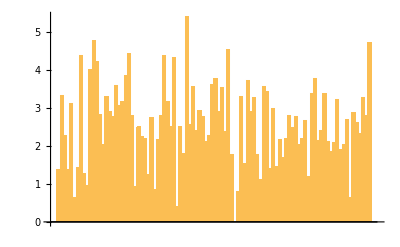

```mathematica
BarChart[nums]
```

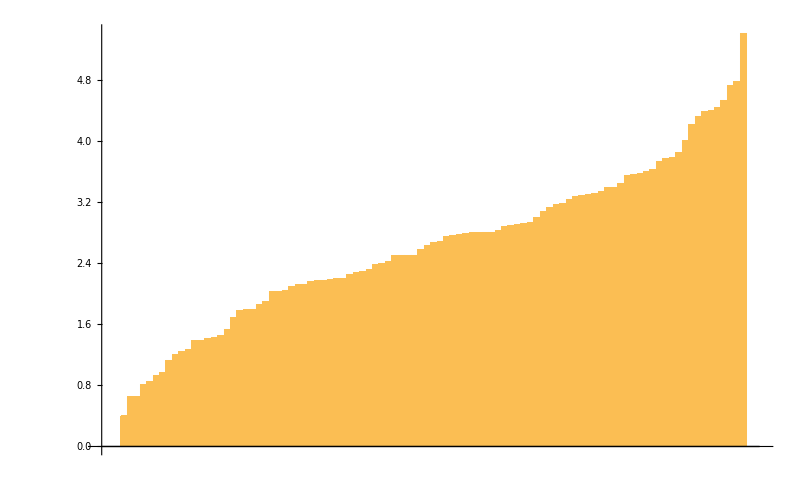

```mathematica
BarChart[Tooltip@@@Reverse[bs,2]]
```